# Vollaro Simone 501740

## Loading and formatting simulation data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["ComputationalGeometry`"]
```

List of xls files in the directory

List of available telemetry files

```mathematica
circuits = FileNames["*.xls"];
Transpose[{Range[Length[circuits]],circuits}]//TableForm
```

1 | Gp2_Barcellona_L1_SIMULATORE.xls
2 | Gp2_Barcellona_L1.xls
3 | Gp2_monza_L1.xls

Import data from file

```mathematica
choosenCircuit = 1;
Laps = Import[circuits[[choosenCircuit]],{"Sheets"}];
```

Total number of laps (in case the xls file has more than one sheet, one for each lap)

```mathematica
totalLaps=Length[Laps]
```

1

Chosen lap

```mathematica
lap = 1;
```

List of data readings conducted

```mathematica
readings= Import[circuits[[choosenCircuit]],{"Data",lap}];
columns =DeleteDuplicates[ Flatten[Map[Position[readings,#]&, {
"Time",
"speed","Speed","SpeedOverGround","Velocita",
"RawAx","AX","Acc_Long","ACC_X",
"RawAy","AY","Acc_Lat","ACC_Y",
"gyro_z","omega_z_vettura","Vel_Imb","YawRate","YAW_RATE",
"steer","Steer","Angolo_Sterzo","steerAngleWheels","FL_TOE",
"beta","BodySlipAngle","VehicleBeta",
"Dist","dist","LAP_DI","LAP_DIST"
}]]];
(*
Part and Span used because Flatten mixes row and column indexes; this way the list will contain only the column indications
*)
```

Import of raw data from file

```mathematica
(*to check that it's imported row by row: Import[circuits[[choosenCircuit]],{"Data", lap, 1, columns}]*)
rawData = Import[circuits[[choosenCircuit]],{"Data",lap,All,columns}];
```

Drop first row, containing only identification tags

```mathematica
channels = Transpose[Drop[rawData,1]];
```

Create separate lists for all imported data

```mathematica
{time,uraw,axraw,ayraw,rraw,δraw,βraw}=channels[[1;;7]];
```

Useful script to round axis units

```mathematica
xgrids[min_,max_]:=Join[{{0,{Black,Thick}}},Table[{j,Dashed},{j,Round[min],Round[max],1}]]
xgrids10[min_,max_]:=Join[{{0,{Black,Thick}}},Table[{j,Dashed},{j,Round[min],Round[max],10}]]
ygrids01[min_,max_]:=Join[{{0,{Black,Thick}}},Table[{j,Dashed},{j,Round[min,0.1],Round[max,0.1],0.1}]]
ygrids001[min_,max_]:=Join[{{0,{Black,Thick}}},Table[{j,Dashed},{j,Round[min,0.01],Round[max,0.01],0.01}]]
xgrids100[min_,max_]:=Join[{{0,{Black,Thick}}},Table[{j,Dashed},{j,Round[min],Round[max],100}]]
ygrids1[min_,max_]:=Join[{{0,{Black,Thick}}},Table[{j,Dashed},{j,Round[min],Round[max],1}]]
ygrids5[min_,max_]:=Join[{{0,{Black,Thick}}},Table[{j,Dashed},{j,Round[min/5]*5,Round[max/5]*5,5}]]
ygrids50[min_,max_]:=Join[{{0,{Black,Thick}}},Table[{j,Dashed},{j,Ceiling[min/50]*50,Ceiling[max/10]*10,50}]]
```

## Data Inspection and manipulation

## Plots to inspect raw data

Comparing with informations on the internet, the longitudinal velocity u_raw seems to be expressed in km/h

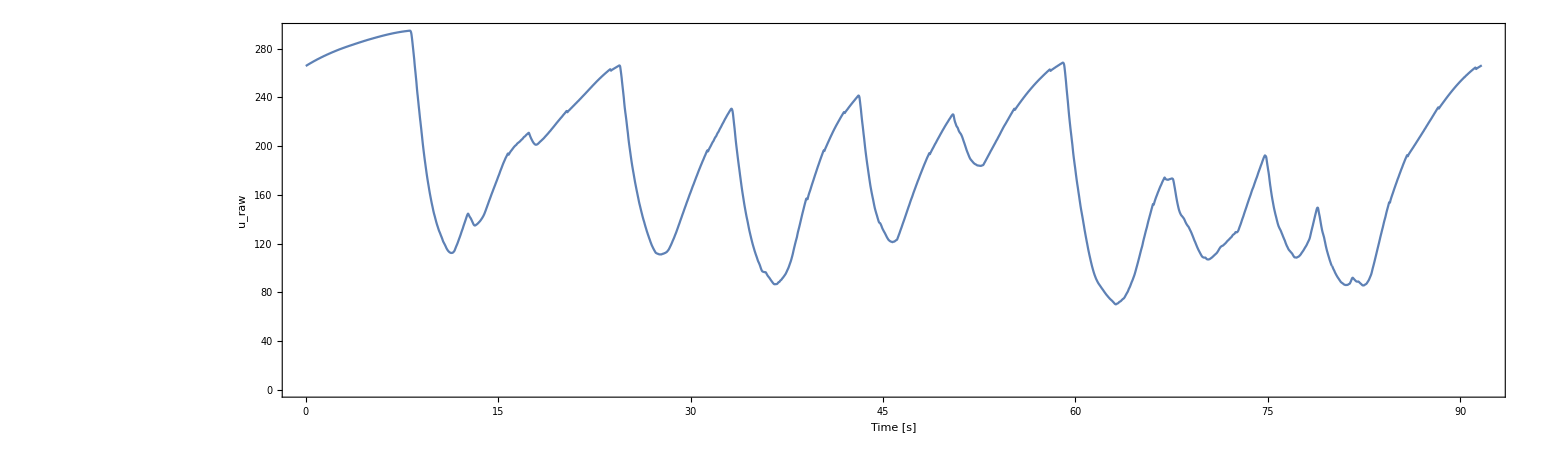

```mathematica
ListLinePlot[Transpose[{time,uraw}],Frame-> True,FrameLabel->{"Time [s]","u_raw"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids50},PlotRange->All,ImageSize->2000,AspectRatio->0.3]
```

Both longitudinal acceleration a_(x,raw) and lateral acceleration a_(y,raw) are approximately in range [-4; 4], so it is fair to assume these are expressed in multiples of the gravity acceleration g = 9.81m/s^2

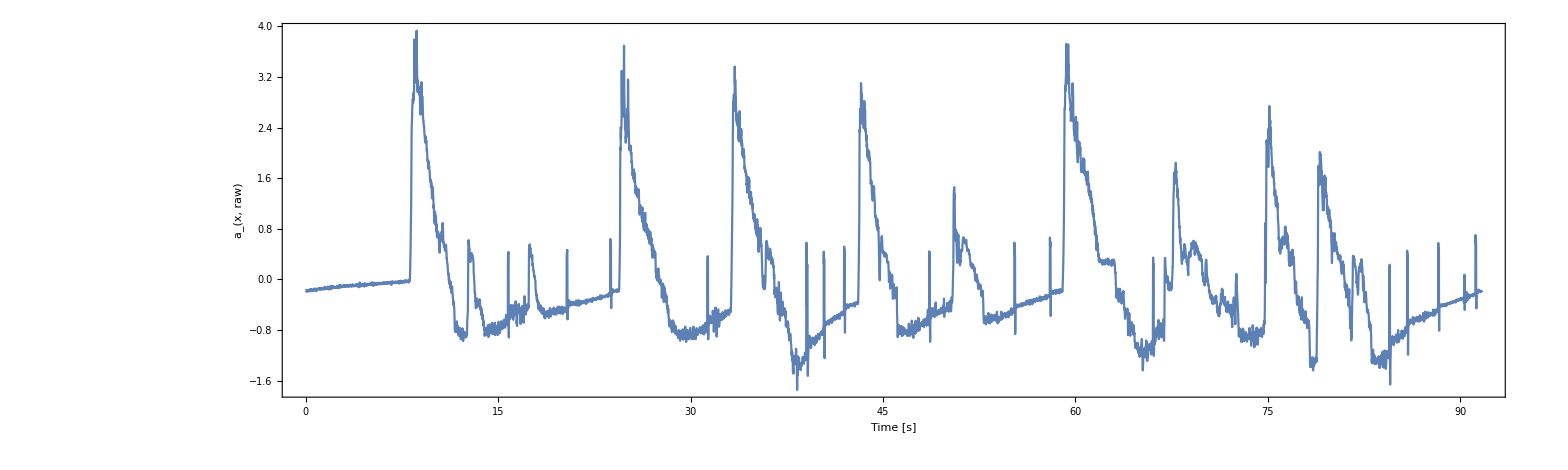

```mathematica
ListLinePlot[Transpose[{time,axraw}],Frame-> True,FrameLabel->{"Time [s]","a_(x, raw)"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1},PlotRange->All,ImageSize->2000,AspectRatio->0.3]
```

a_y isconsideredpositiveforleftturns,negativeforrightones

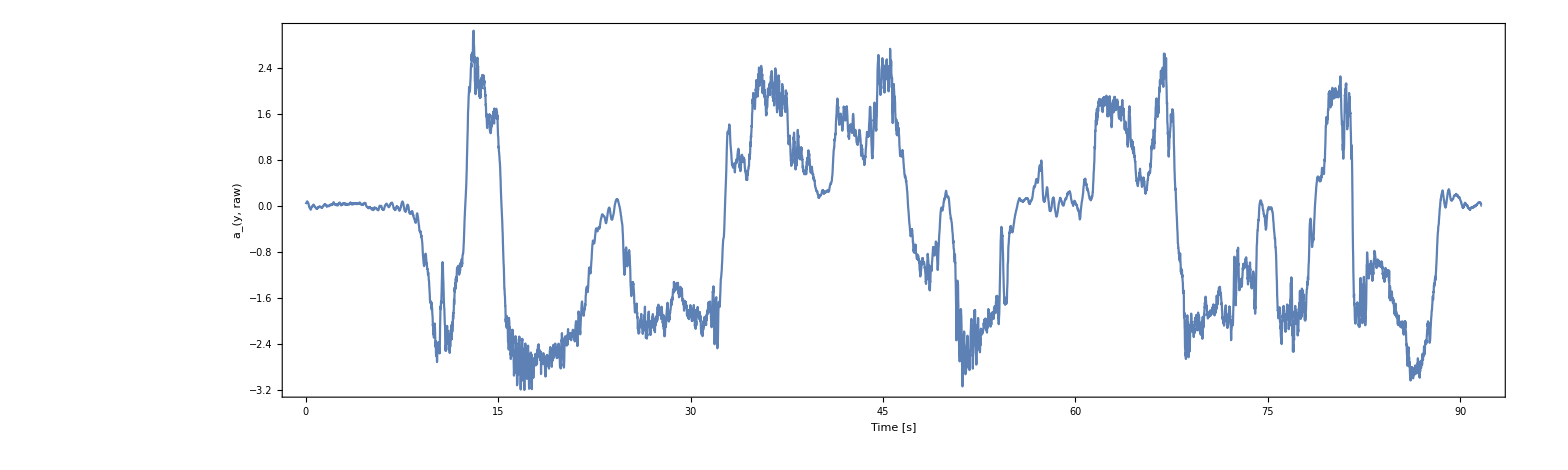

```mathematica
ListLinePlot[Transpose[{time,ayraw}],Frame-> True,FrameLabel->{"Time [s]","a_(y, raw)"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1},PlotRange->All,ImageSize->2000,AspectRatio->0.3]
```

Given that a negative longitudinal acceleration a_x would mean for the longitudinal velocity u to decrease, from the plot beneath we can infer that data for a_(x,raw) have an inverse sign; it is worth noting how sharp are the transitions whenever a braking application begins.

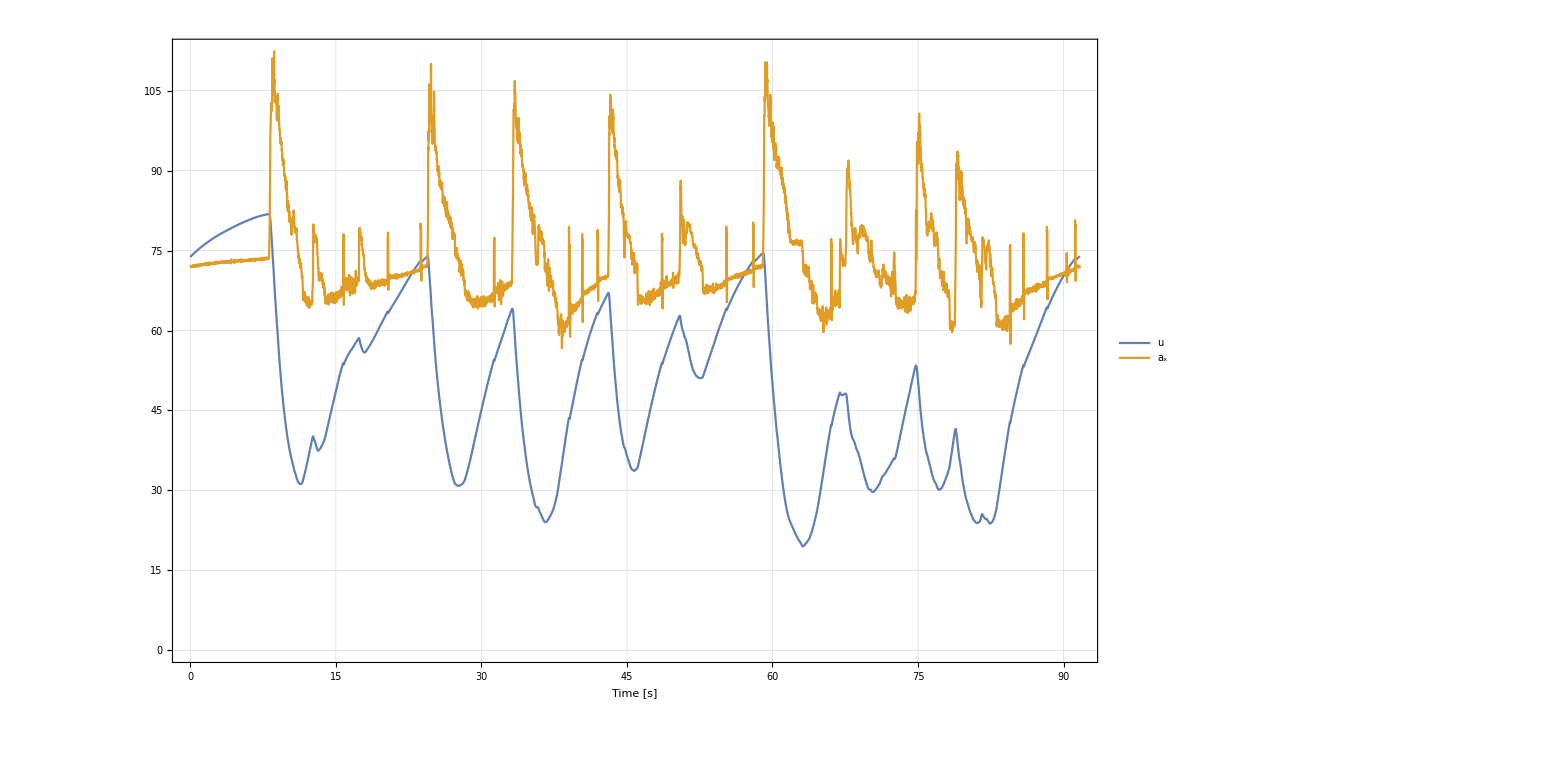

```mathematica
ListLinePlot[{Transpose[{time,uraw/3.6}],Transpose[{time,axraw*9.81+uraw[[1]]/3.6}]},PlotRange->All,ImageSize->2000,AspectRatio->0.5,Frame-> True,PlotLegends-> Placed[{"u","a_x"},Top],GridLines->{xgrids,ygrids5},FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large]]
```

Given the lateral acceleration in steady-state conditions a_y= u×r, we can see from the plot beneath that the yaw rate  r_raw has been measured with opposite sign compared to the convention (right-hand convention also applies, and the first curve is a right-hand turn). Unit of measure seems to be radians.

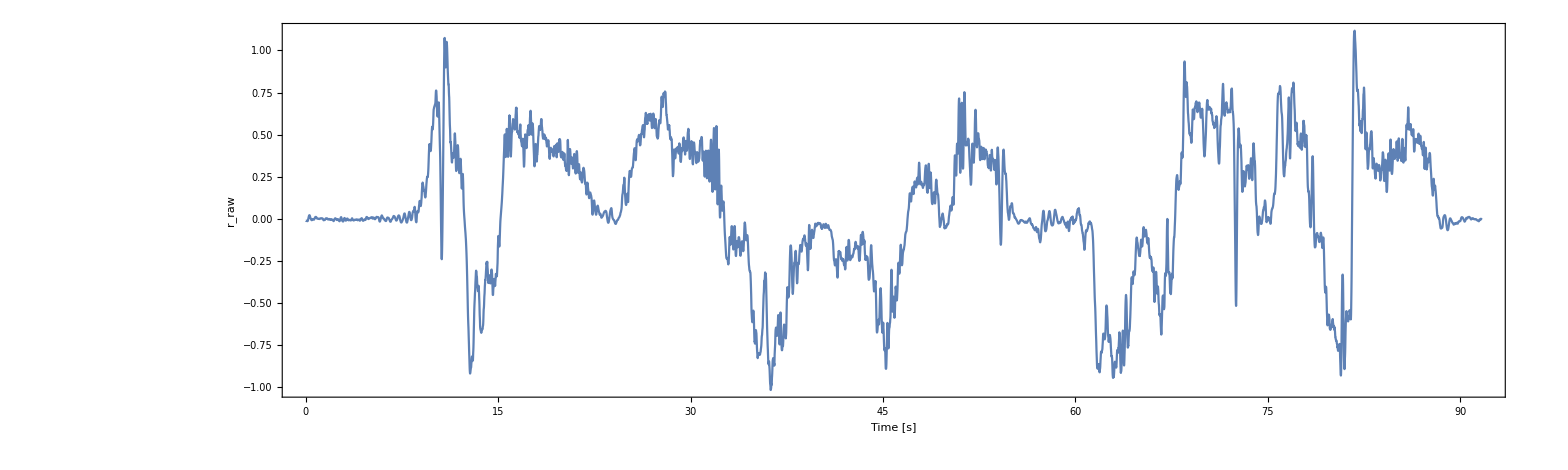

```mathematica
ListLinePlot[Transpose[{time,rraw}],PlotRange->All,ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","r_raw"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids01}]
```

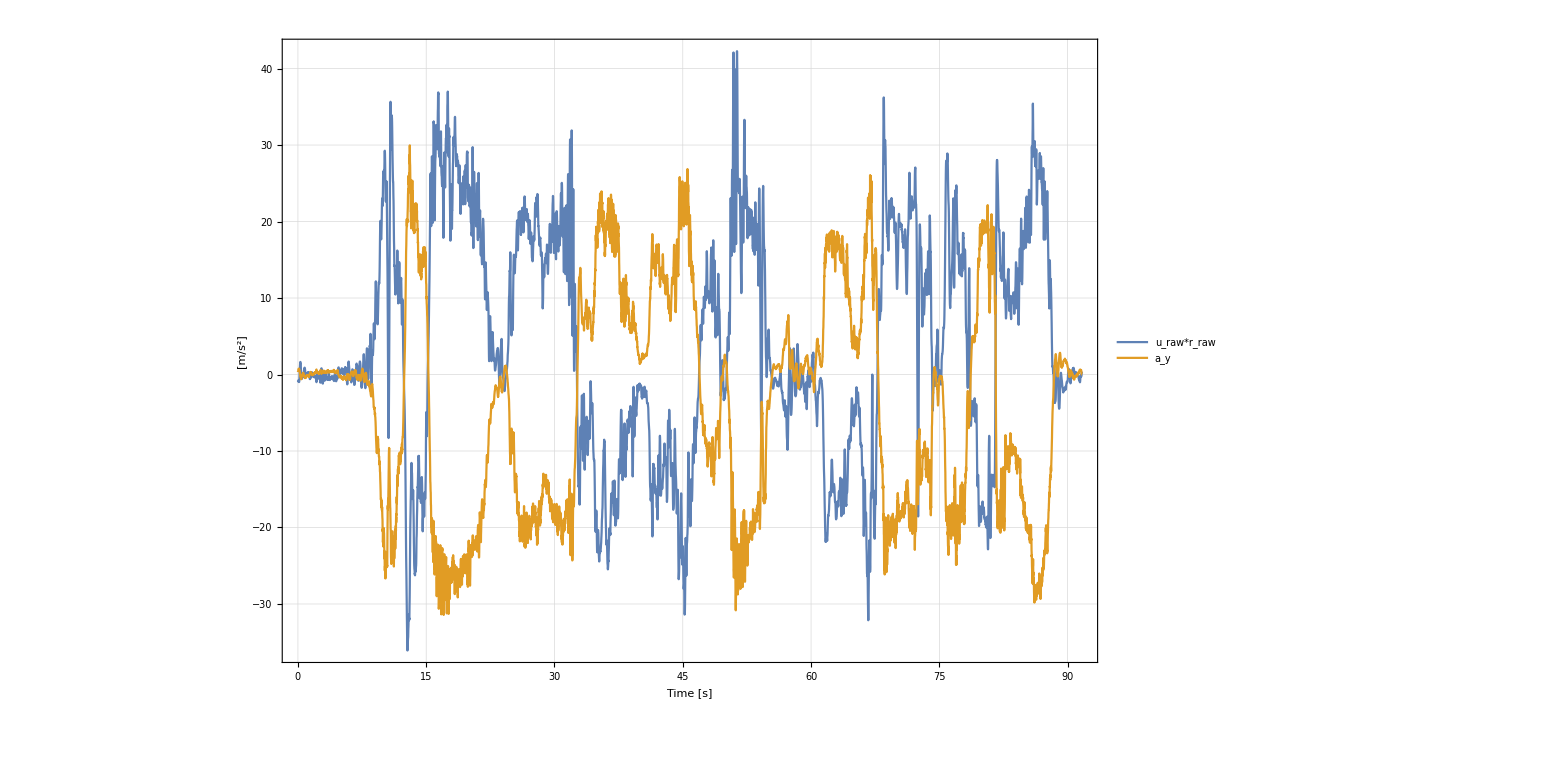

```mathematica
ListLinePlot[{Transpose[{time,uraw/3.6*rraw}],Transpose[{time,ayraw*9.81}]},PlotRange->All,ImageSize->2000,AspectRatio->0.5,PlotLegends->Placed[{"u_raw*r_raw","a_y"},Top],Frame->True,GridLines->{xgrids,ygrids5},FrameLabel->{"Time [s]","[m/s^2]"},LabelStyle->Directive[Black,Bold,Large]]
```

Angles β and δ are measured in radians and with opposite sign: the first curve is a right-hand turn, thus δ should be negative and β positive.

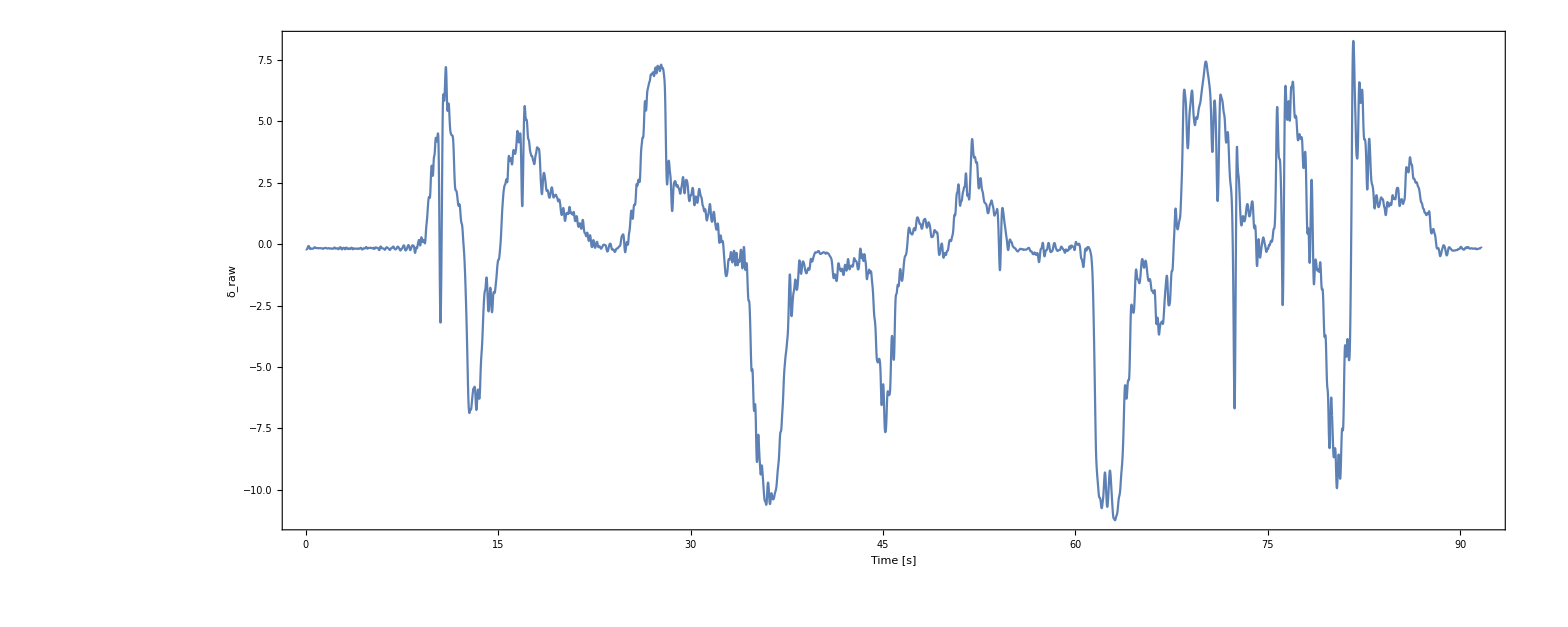

```mathematica
ListLinePlot[Transpose[{time,δraw}],PlotRange->All,ImageSize->2000,AspectRatio->Automatic,Frame-> True,FrameLabel->{"Time [s]","δ_raw"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

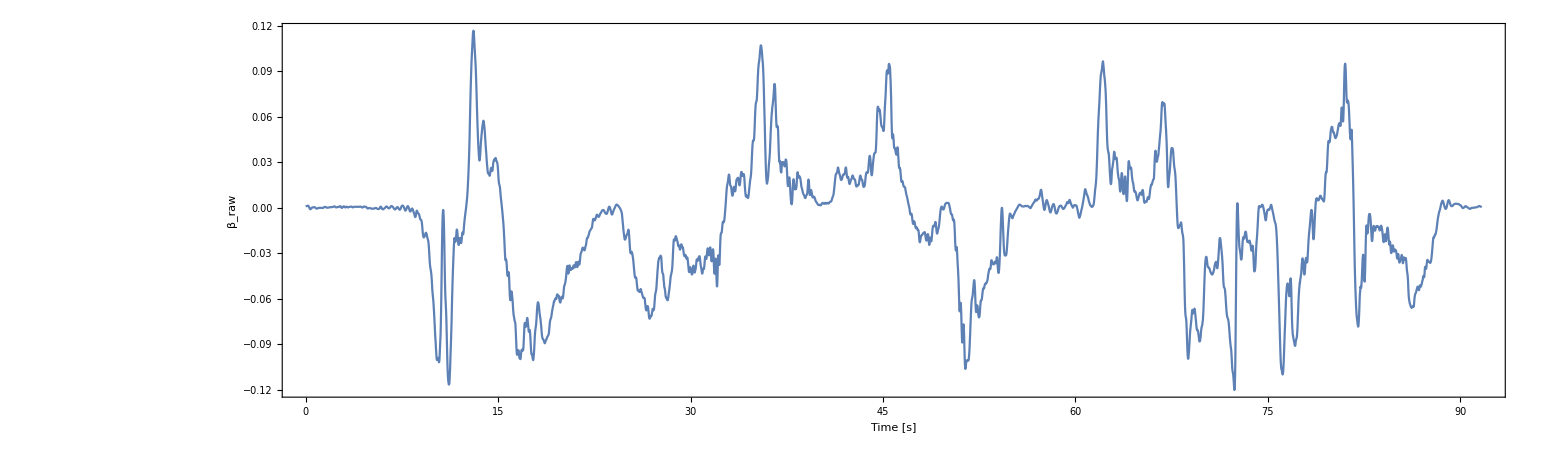

```mathematica
ListLinePlot[Transpose[{time,βraw}],PlotRange -> All, ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","β_raw"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids001}]
```

Comparison of yaw rate r (amplified in the plot beneath) and steering angle δ, both corrected. A positive steering angle means for the vehicle to turn left, which should be reflected on the yaw rate (and vice versa).

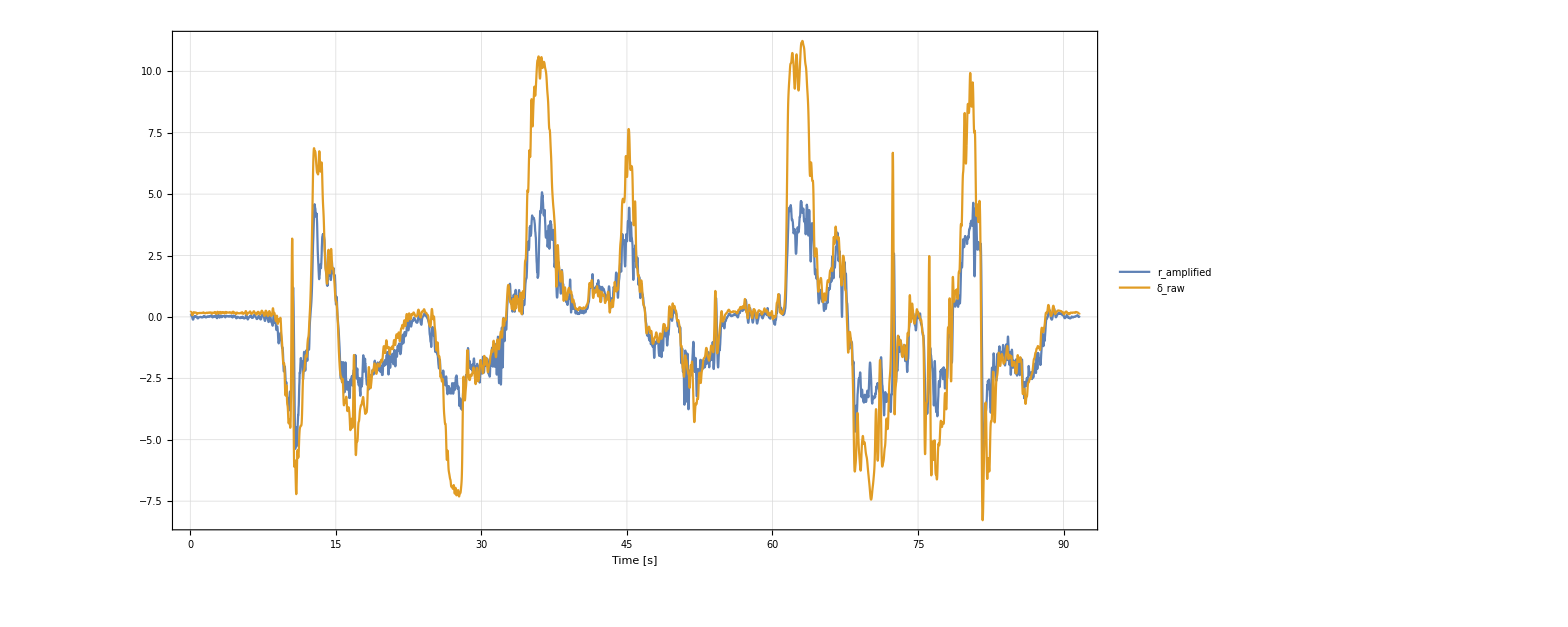

```mathematica
ListLinePlot[{Transpose[{time,-5rraw}],Transpose[{time,-δraw}]},PlotLegends->Placed[{"r_amplified","δ_raw"},Top],PlotRange->All,ImageSize->3000,AspectRatio->Automatic,Frame-> True,FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

From the imported data, we can also gather the lateral velocity
v = u × tan(β)

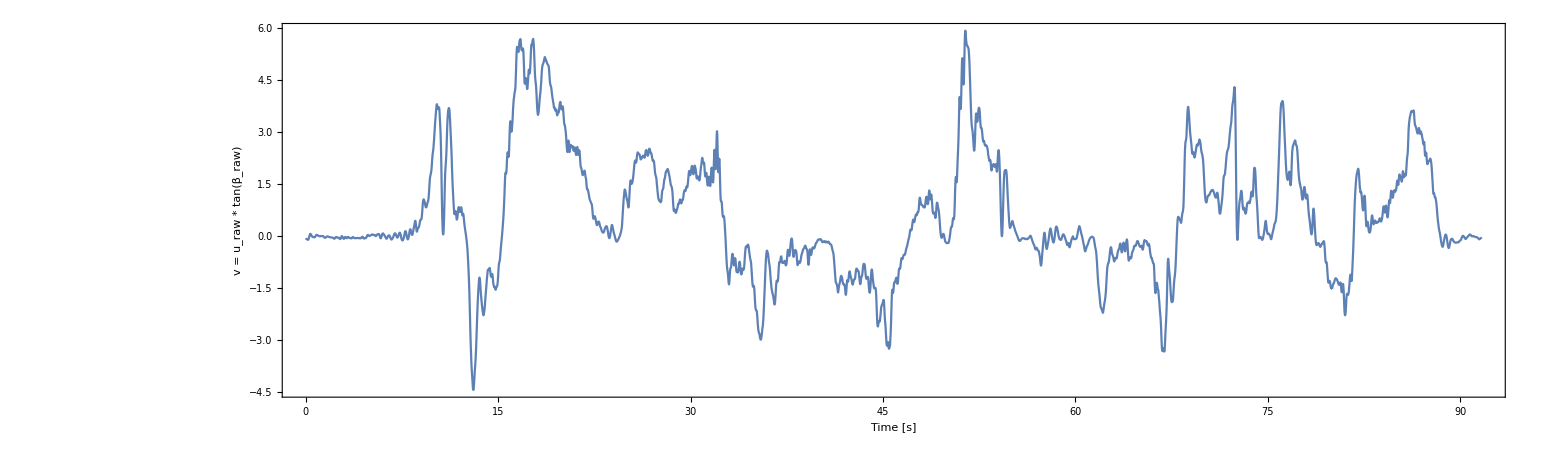

```mathematica
ListLinePlot[Transpose[{time,uraw/3.6*Tan[-βraw]}],PlotRange->All,ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","v = u_raw * tan(β_raw)"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

## Rightly formatted telemetry data, with some computations

Lists of all quantities, in IS units:
[s, m/s, m/s^2,m/s^2, rad/s, rad, rad, m/s]

```mathematica
telemetry={time,uraw/3.6,-axraw*9.81,ayraw*9.81,-rraw,-δraw,-βraw,uraw/3.6*Tan[-βraw]};
{time, utel,axtel,aytel,rtel,δtel,βtel,vtel} = telemetry;
```

From the yaw rate we can obtain the yaw angle of the vehicle by means of a discrete integration; since data is gathered every 0.01s, we can compute a discrete-time integration as follows

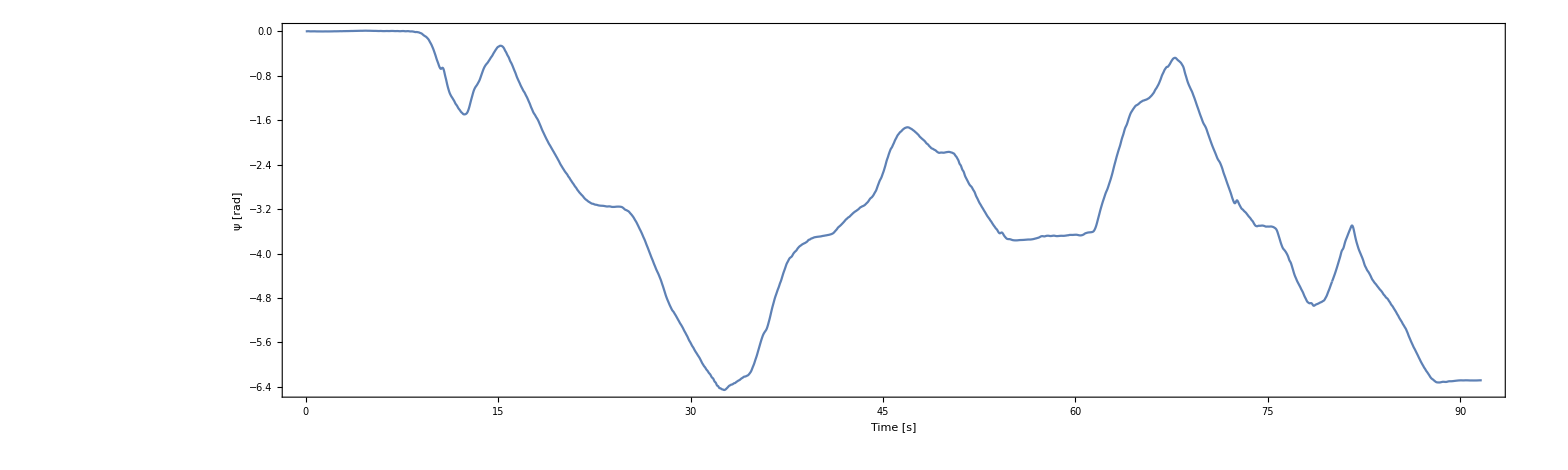

```mathematica
yawtel=Accumulate[rtel]/100;
ListLinePlot[Transpose[{time,yawtel}],PlotRange->All,ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","ψ [rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

At first glance, the yaw angle (usually labeled as ψ) seems to indicate that the vehicle is performing a clockwise lap of the circuit.

Computation of tangential and normal/centripetal acceleration

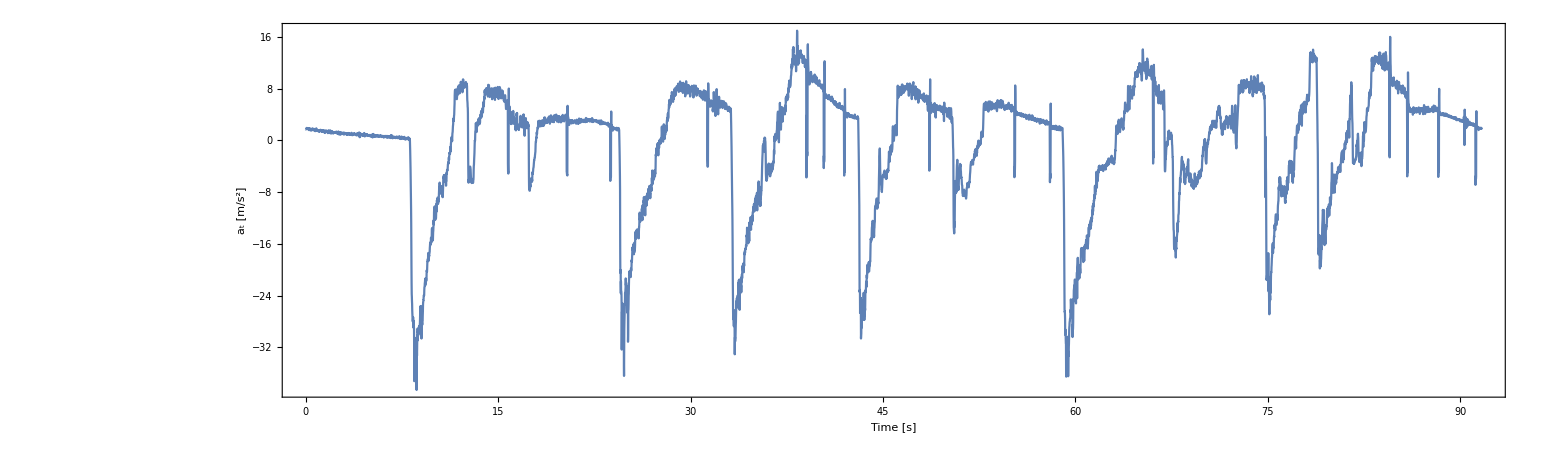

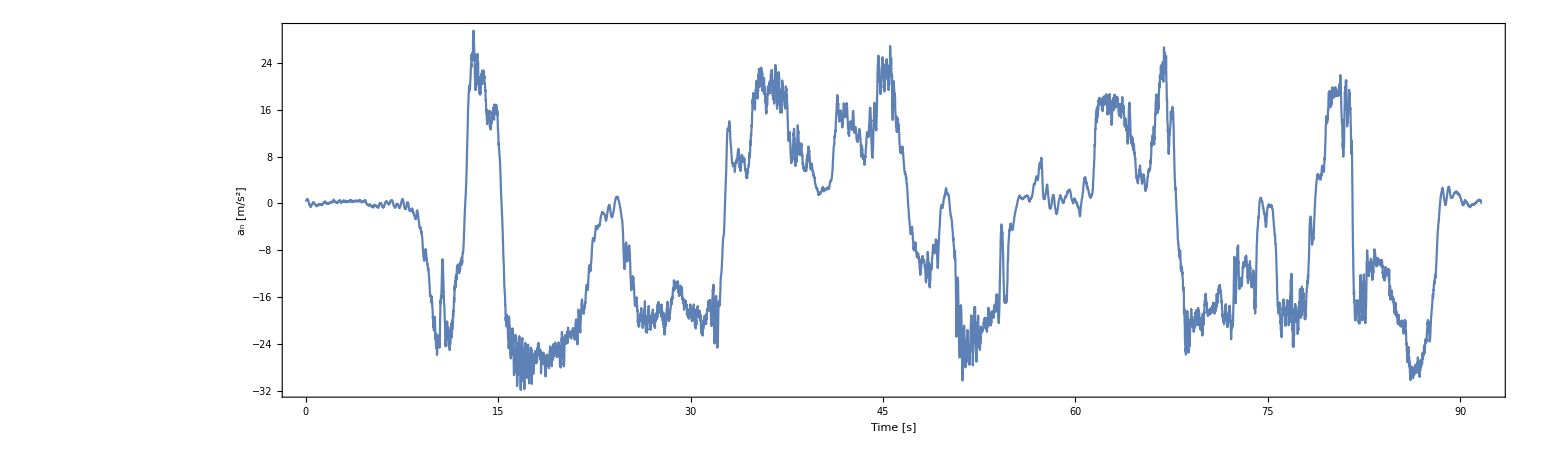

```mathematica
attel = aytel*Sin[βtel]+axtel*Cos[βtel];
antel = aytel*Cos[βtel]-axtel*Sin[βtel];
ListLinePlot[Transpose[{time,attel}],ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","a_t [m/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
ListLinePlot[Transpose[{time,antel}],ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","a_n [m/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
```

## Filtering data

Spectral analysis to ensure chosen filter bandwidth is consistent with frequency components of the signals

```mathematica
frequencies[data_,Fs_] := (Range[Length[data]]-Ceiling[Length[data]/2])/Fs;
```

```mathematica
spectrum[data_]:= RotateRight[Abs[Fourier[data]]^2,Ceiling[Length[data]/2]-1];
```

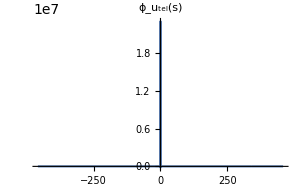
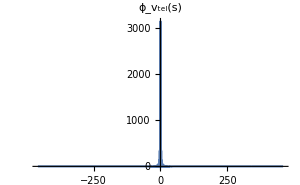
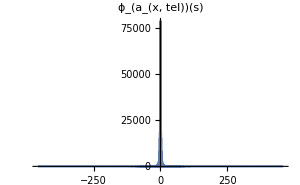
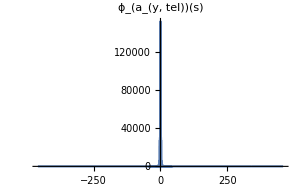
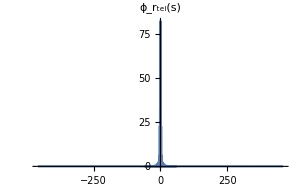
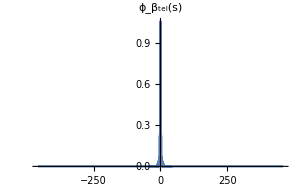
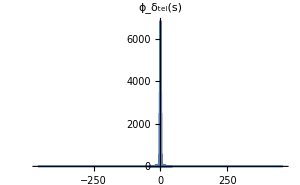

```mathematica
Row[{
	ListLinePlot[Transpose[{frequencies[axtel,10],spectrum[utel]}],PlotRange->All,ImageSize->300,PlotLabel->"ϕ_u_tel(s)"],
	ListLinePlot[Transpose[{frequencies[axtel,10],spectrum[vtel]}],PlotRange->All,ImageSize->300,PlotLabel->"ϕ_v_tel(s)"],
	ListLinePlot[Transpose[{frequencies[axtel,10],spectrum[axtel]}],PlotRange->All,ImageSize->300,PlotLabel->"ϕ_(a_(x, tel))(s)"],
	ListLinePlot[Transpose[{frequencies[axtel,10],spectrum[aytel]}],PlotRange->All,ImageSize->300,PlotLabel->"ϕ_(a_(y, tel))(s)"],
	ListLinePlot[Transpose[{frequencies[axtel,10],spectrum[rtel]}],PlotRange->All,ImageSize->300,PlotLabel->"ϕ_r_tel(s)"],
	ListLinePlot[Transpose[{frequencies[axtel,10],spectrum[βtel]}],PlotRange->All,ImageSize->300,PlotLabel->"ϕ_β_tel(s)"],
	ListLinePlot[Transpose[{frequencies[axtel,10],spectrum[δtel]}],PlotRange->All,ImageSize->300,PlotLabel->"ϕ_δ_tel(s)"]
}]
```

We have a data sample every 0.01s, so we can assume a sampling frequency f_sampling = 100 Hz.
We’ll use a low-pass filter to smooth the data.
Note that we could use a Butterworth filter here, but we decided for the FIR-base LowpassFilter for ease of expression.

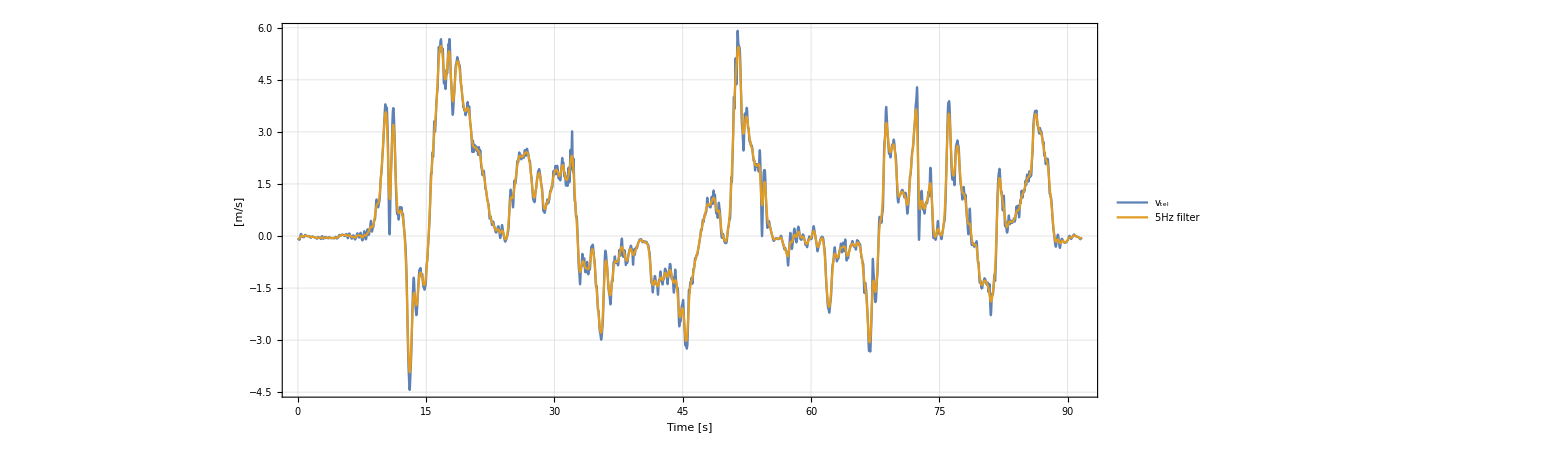

```mathematica
vfil=LowpassFilter[vtel,5,SampleRate->100];
ListLinePlot[{Transpose[{time,vtel}],Transpose[{time,vfil}]},ImageSize->2000,AspectRatio->0.3,PlotLegends->Placed[{"v_tel","5Hz filter"},Top],Frame-> True,FrameLabel->{"Time [s]","[m/s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

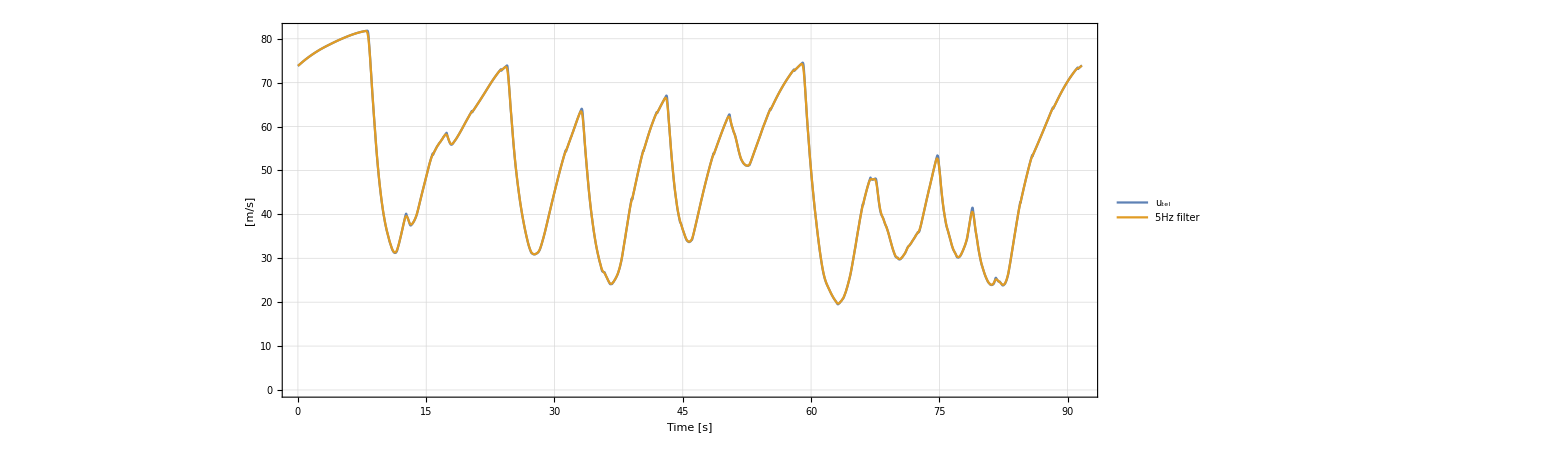

```mathematica
ufil = LowpassFilter[utel,5,SampleRate->100];
ListLinePlot[{Transpose[{time,utel}],Transpose[{time,ufil}]},ImageSize->2000,AspectRatio->0.3,PlotLegends->Placed[{"u_tel","5Hz filter"},Top],Frame-> True,FrameLabel->{"Time [s]","[m/s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
```

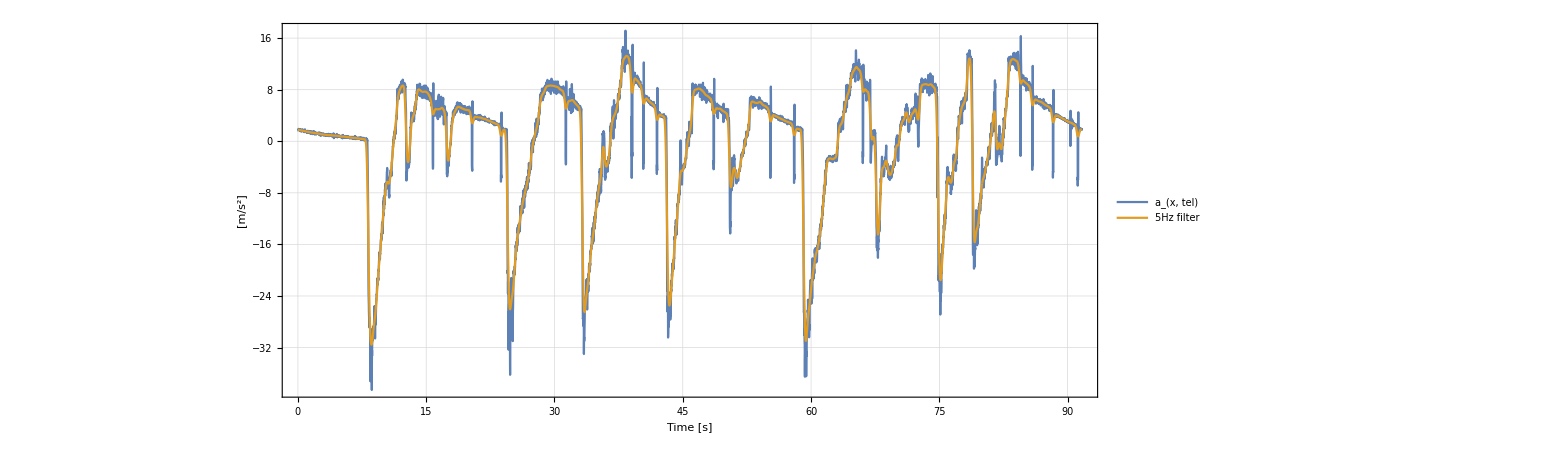

```mathematica
axfil = LowpassFilter[axtel,5,SampleRate->100];
ListLinePlot[{Transpose[{time,axtel}],Transpose[{time,axfil}]},ImageSize->2000,AspectRatio->0.3,PlotLegends->Placed[{"a_(x, tel)","5Hz filter"},Top],PlotRange->All,Frame-> True,FrameLabel->{"Time [s]","[m/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
```

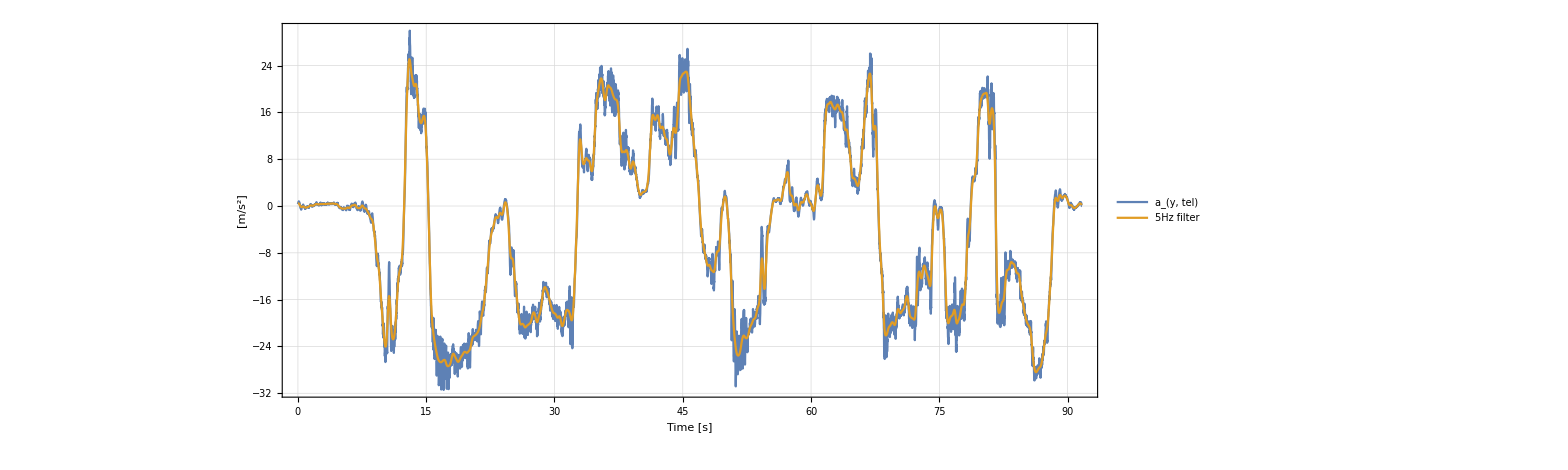

```mathematica
ayfil = LowpassFilter[aytel,5,SampleRate->100];
ListLinePlot[{Transpose[{time,aytel}],Transpose[{time,ayfil}]},ImageSize->2000,AspectRatio->0.3,PlotLegends->Placed[{"a_(y, tel)","5Hz filter"},Top],Frame-> True,FrameLabel->{"Time [s]","[m/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
```

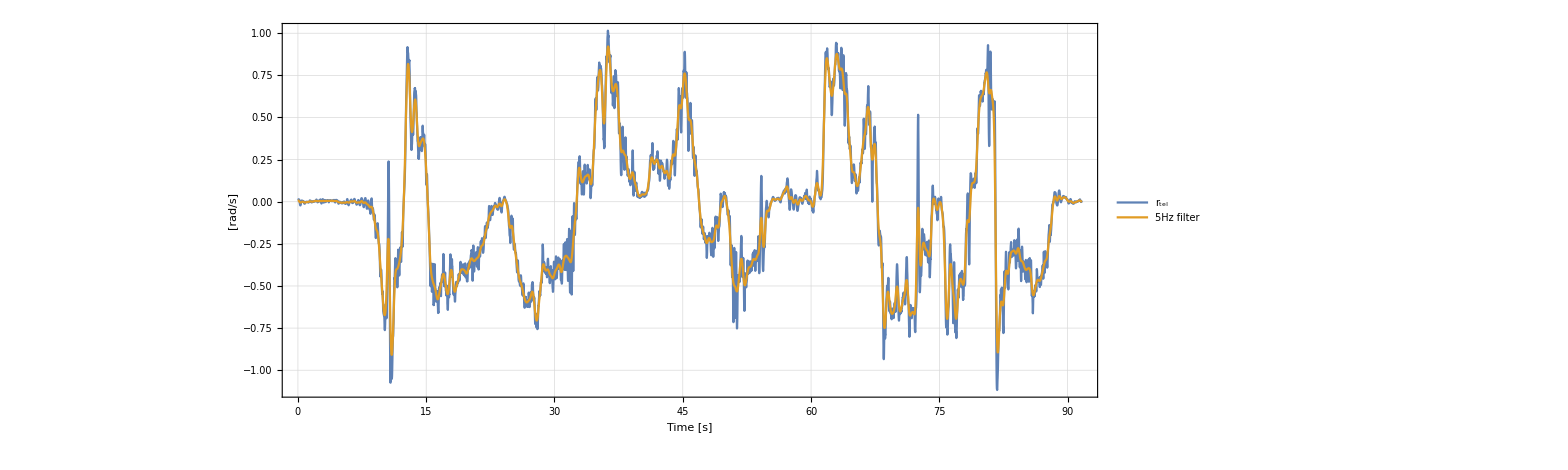

```mathematica
rfil=LowpassFilter[rtel,5,SampleRate->100];
ListLinePlot[{Transpose[{time,rtel}],Transpose[{time,rfil}]},PlotLegends->Placed[{"r_tel", "5Hz filter"},Top],ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","[rad/s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids01}]
```

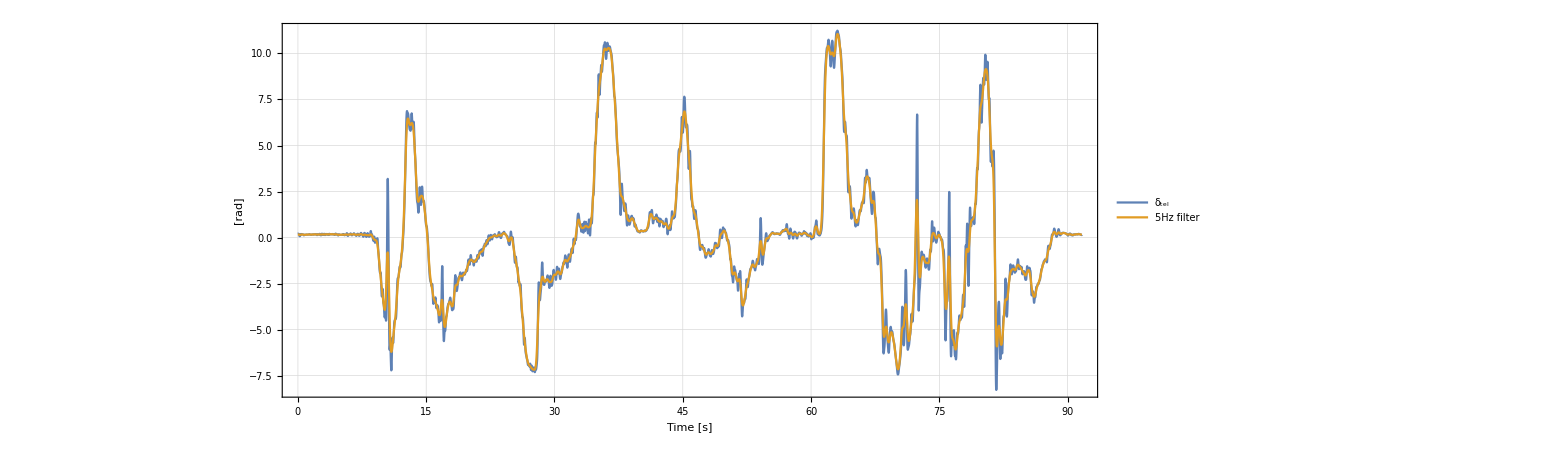

```mathematica
δfil =LowpassFilter[δtel,5,SampleRate->100];
ListLinePlot[{Transpose[{time,δtel}],Transpose[{time,δfil}]},ImageSize-> 2000,AspectRatio-> 0.3,PlotLegends->Placed[{"δ_tel","5Hz filter"},Top],Frame-> True,FrameLabel->{"Time [s]","[rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

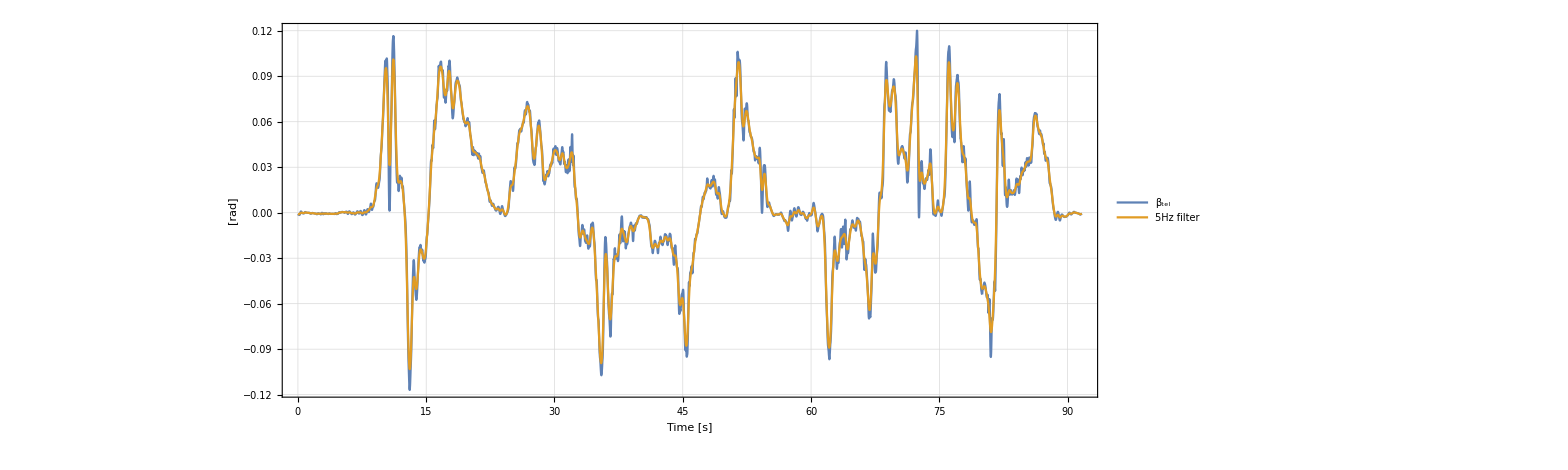

```mathematica
βfil =LowpassFilter[βtel,5,SampleRate->100];
ListLinePlot[{Transpose[{time,βtel}],Transpose[{time,βfil}]},ImageSize-> 2000,AspectRatio-> 0.3,PlotLegends->Placed[{"β_tel","5Hz filter"},Top],Frame-> True,FrameLabel->{"Time [s]","[rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids001}]
```

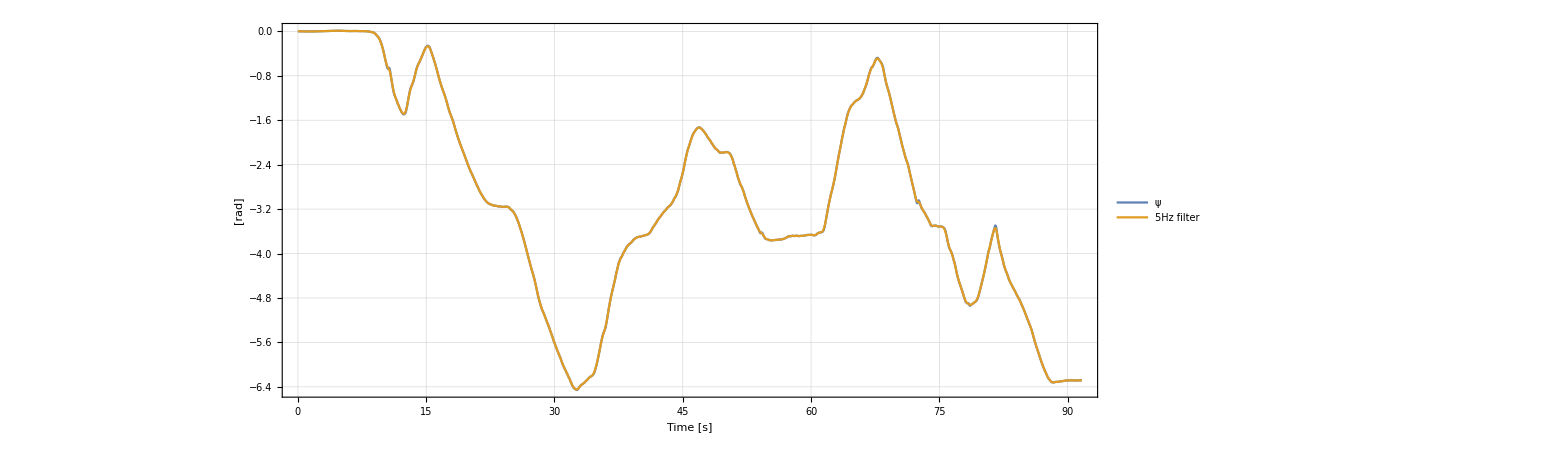

```mathematica
yawfil =LowpassFilter[yawtel,5,SampleRate->100];
ListLinePlot[{Transpose[{time,yawtel}],Transpose[{time,yawfil}]},ImageSize->2000,AspectRatio->0.3,PlotLegends->Placed[{"ψ","5Hz filter"},Top],Frame-> True,FrameLabel->{"Time [s]","[rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

## Interpolated functions

Interpolation functions to get continuous-time functions describing gathered data evolution

```mathematica
ax = Interpolation[Transpose[{time,axtel}],InterpolationOrder->1];
ay = Interpolation[Transpose[{time,aytel}],InterpolationOrder->1];
u = Interpolation[Transpose[{time,utel}],InterpolationOrder->1];
v = Interpolation[Transpose[{time,vtel}],InterpolationOrder->1];
r = Interpolation[Transpose[{time,rtel}],InterpolationOrder->1];
β = Interpolation[Transpose[{time,βtel}],InterpolationOrder->1];
```

## Telemetry study

## Yaw rate study

Differentiation and integration of the filtered yaw rate, and relative plots.

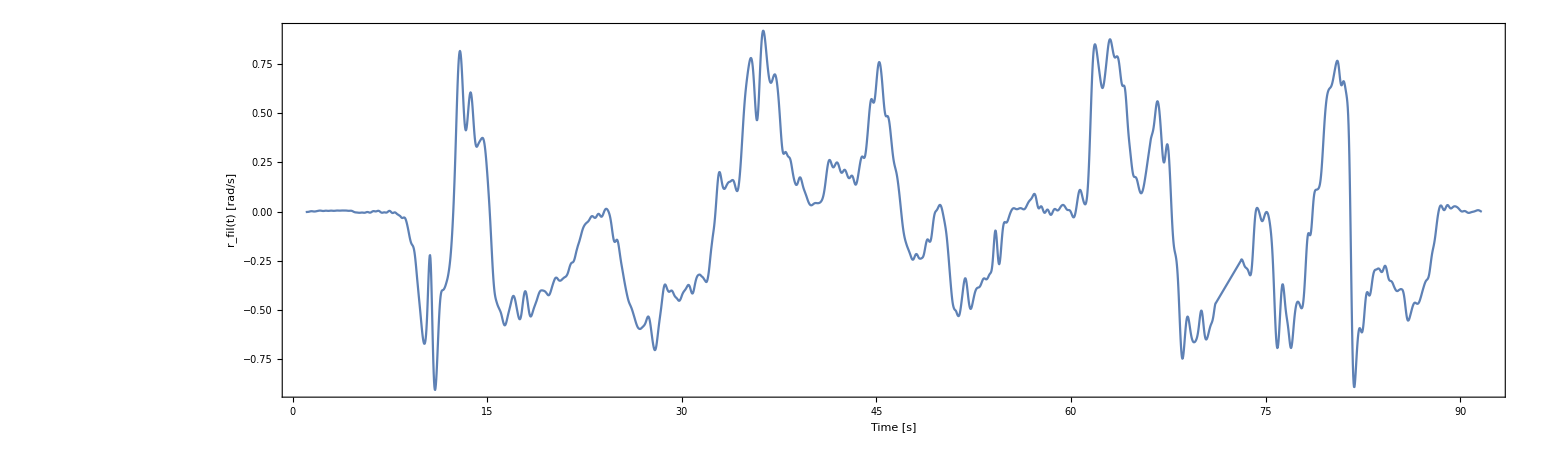

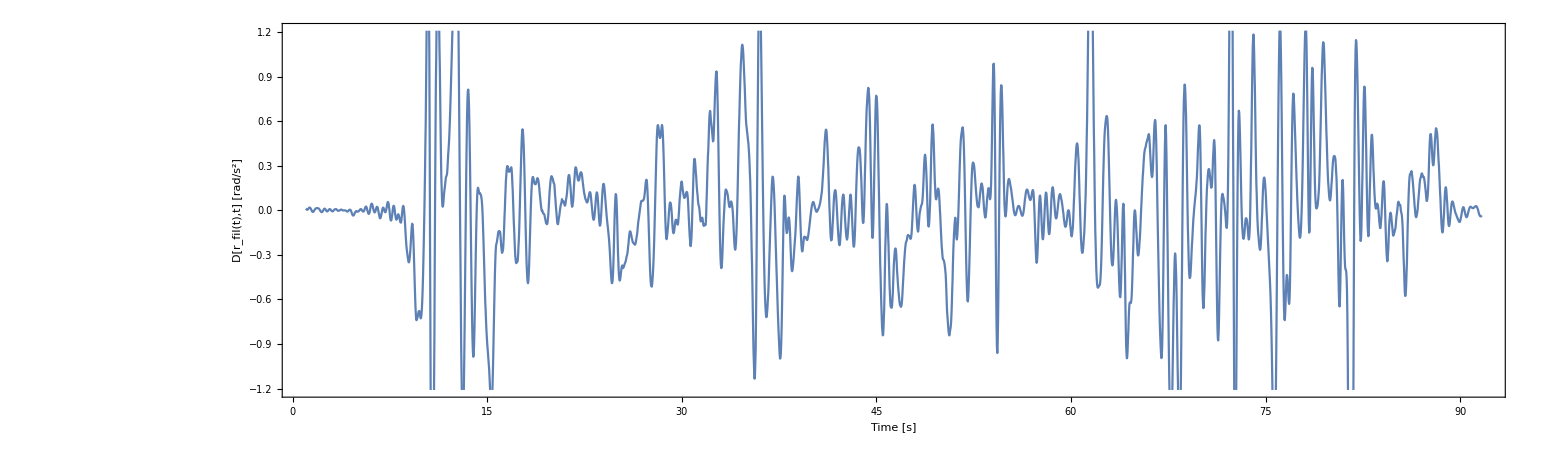

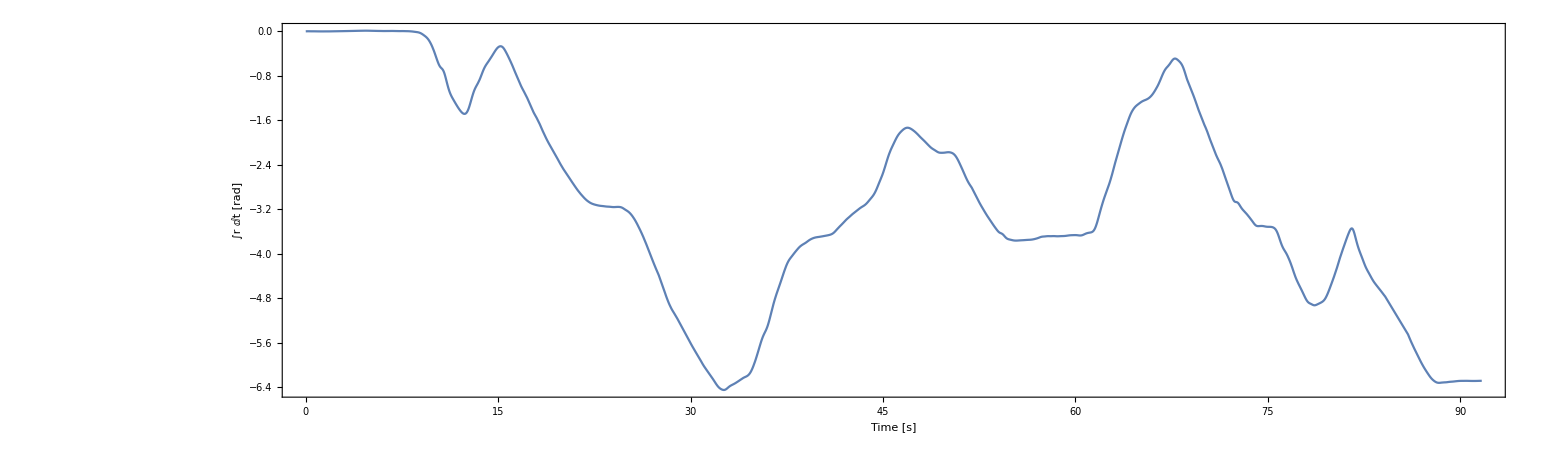

```mathematica
rfilT[t_]=Interpolation[Transpose[{time,rfil}],InterpolationOrder->1][t];
rfilDot[t_]=D[rfilT[t],t];
rfilInt[t_] = Integrate[rfilT[t],t];
rDotfil = rfilDot@ValuesOnGrid;
Plot[rfilT[t],{t,1,Last[time]}, ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","r_fil(t) [rad/s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids01}]
Plot[rfilDot[t],{t,1,Last[time]}, ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","D[r_fil(t),t] [rad/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
Plot[rfilInt[t],{t,0,Last[time]},PlotRange->All,ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","∫r ⅆt [rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

## Slip angle study

Radius of curvature R_G and curvature ρ_G of the center of mass of the vehicle.

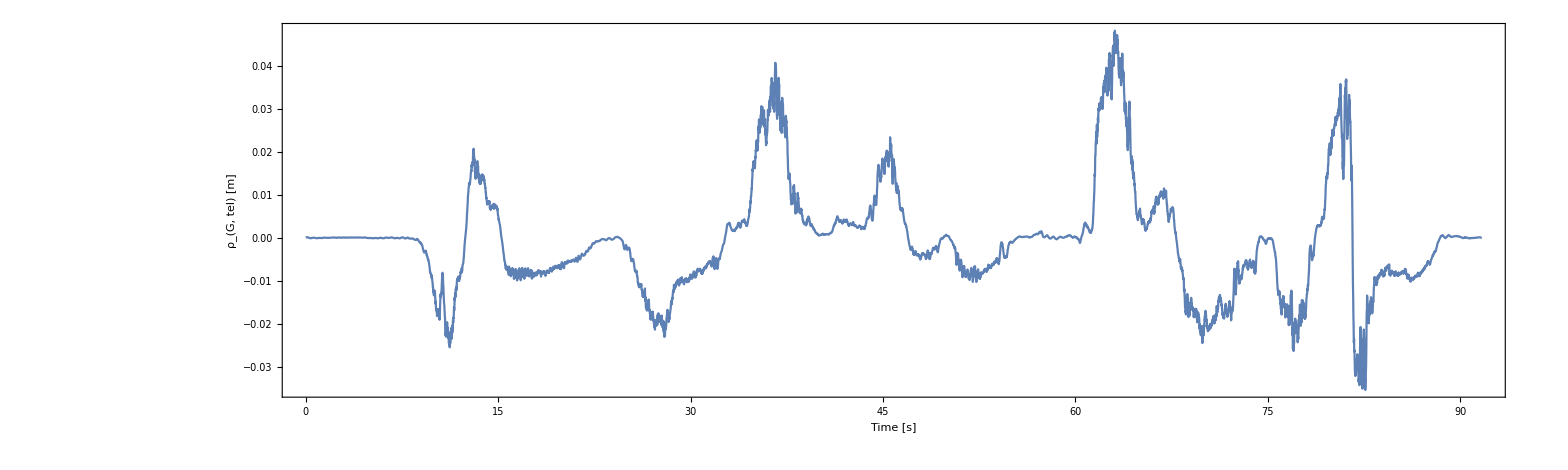

```mathematica
RcurvG = utel^2/antel;
ρGtel = antel/utel^2;
ListLinePlot[Transpose[{time,ρGtel}],ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]","ρ_(G, tel) [m]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids001},PlotRange->All]
```

Derivative of the ratio β, used as an approximation of the slip angle β̂:
β̂=arctan(β)≈β, if β<10°
Used formula page 78 SVD for β̇ → ρ_G≃(r+β̇)/u

```mathematica
βDottel = utel*ρGtel-rtel;
```

As we can see in the plots beneath, to get a “good” approximation of β from ρ_G≃(r+β̇)/u we have to implement two kind of noise-removing filters, a HighpassFilter and a LowpassFilter, and apply them to two different subsets of the acquired data.

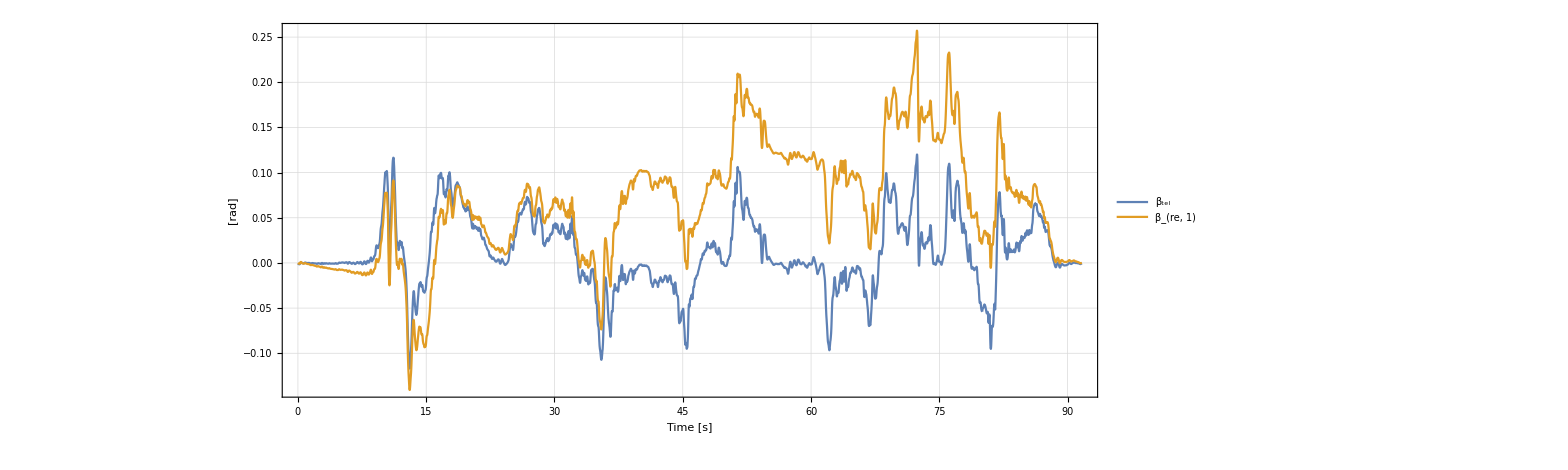

```mathematica
βre1 = Accumulate[βDottel-HighpassFilter[βDottel,100,SampleRate->100]-Mean[βDottel]]/100;
ListLinePlot[{Transpose[{time,βtel}],Transpose[{time,βre1}]},PlotLegends->Placed[{"β_tel","β_(re, 1)"},Top],ImageSize->2000,AspectRatio->0.3,PlotRange->All,Frame->True,FrameLabel->{"Time [s]","[rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids01}]
```

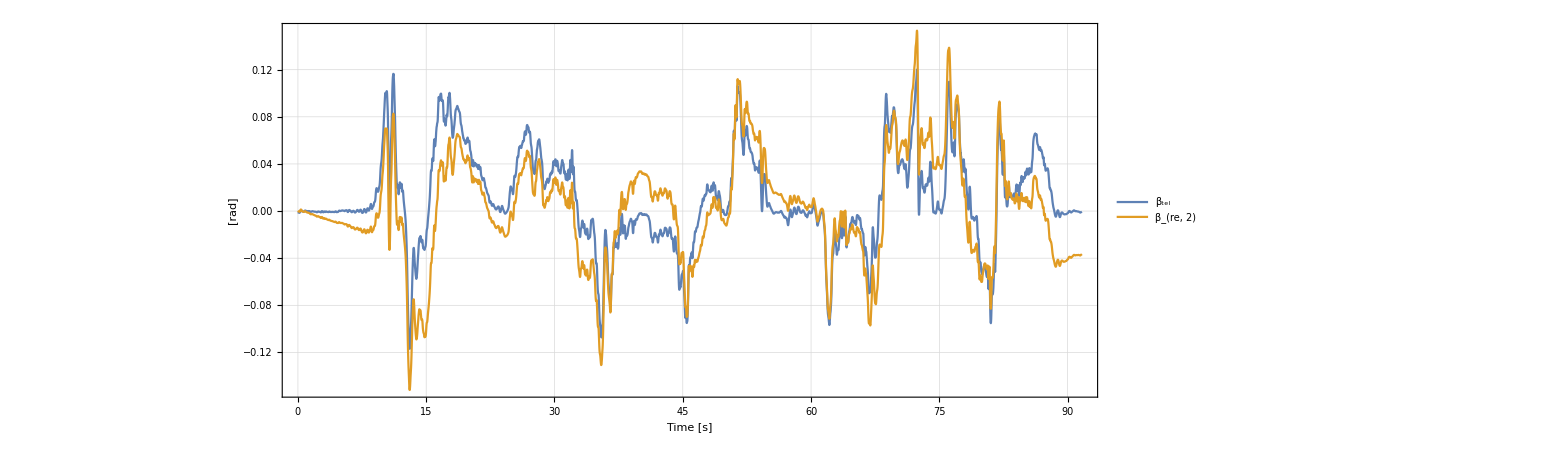

```mathematica
βre2 = βre1-LowpassFilter[βre1,0.1,9000,SampleRate->100];
ListLinePlot[{Transpose[{time,βtel}],Transpose[{time,βre2}]},PlotLegends->Placed[{"β_tel","β_(re, 2)"},Top],ImageSize->2000,AspectRatio->0.3,PlotRange->All,Frame->True,FrameLabel->{"Time [s]","[rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids001}]
```

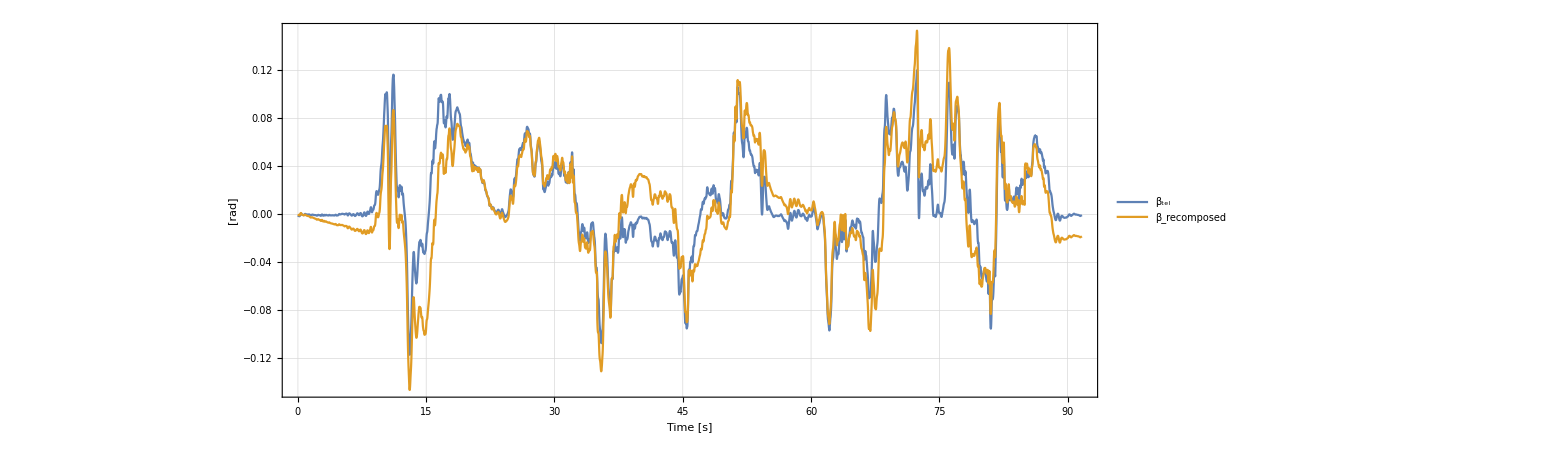

```mathematica
βrecomposed = Join[(βre2[[1;;3500]]+βre1[[1;;3500]])/2,βre2[[3501;;8500]],(βre2[[8501;;All]]+βre1[[8501;;All]])/2];
ListLinePlot[{Transpose[{time,βtel}],Transpose[{time,βrecomposed}]},PlotLegends->Placed[{"β_tel","β_recomposed"},Top],ImageSize->2000,AspectRatio->0.3,PlotRange->All,Frame->True,FrameLabel->{"Time [s]","[rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids001}]
```

## Lateral velocity study

Comparison of lateral velocity data and approximation given by a_y=v̇+ur

```mathematica
latVelDottel = aytel-utel*rtel;
```

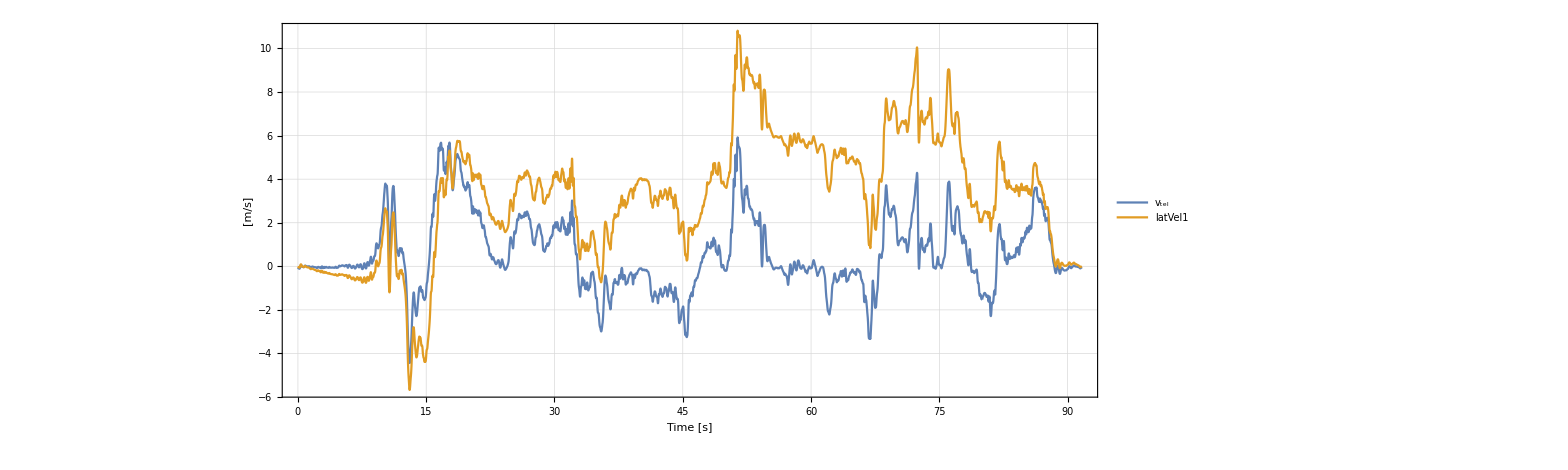

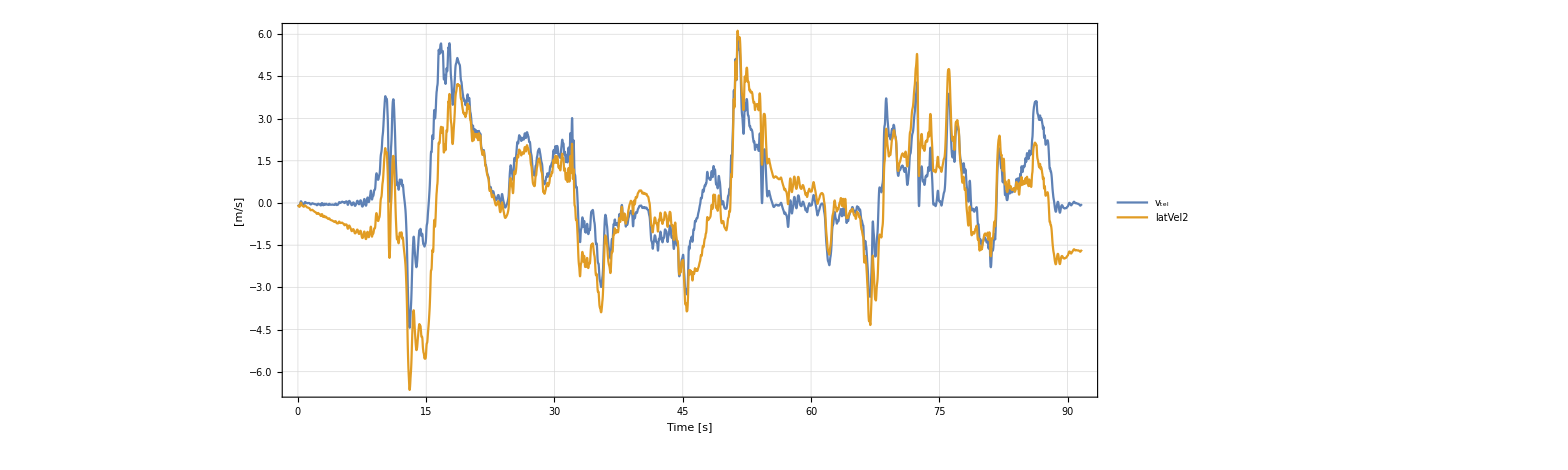

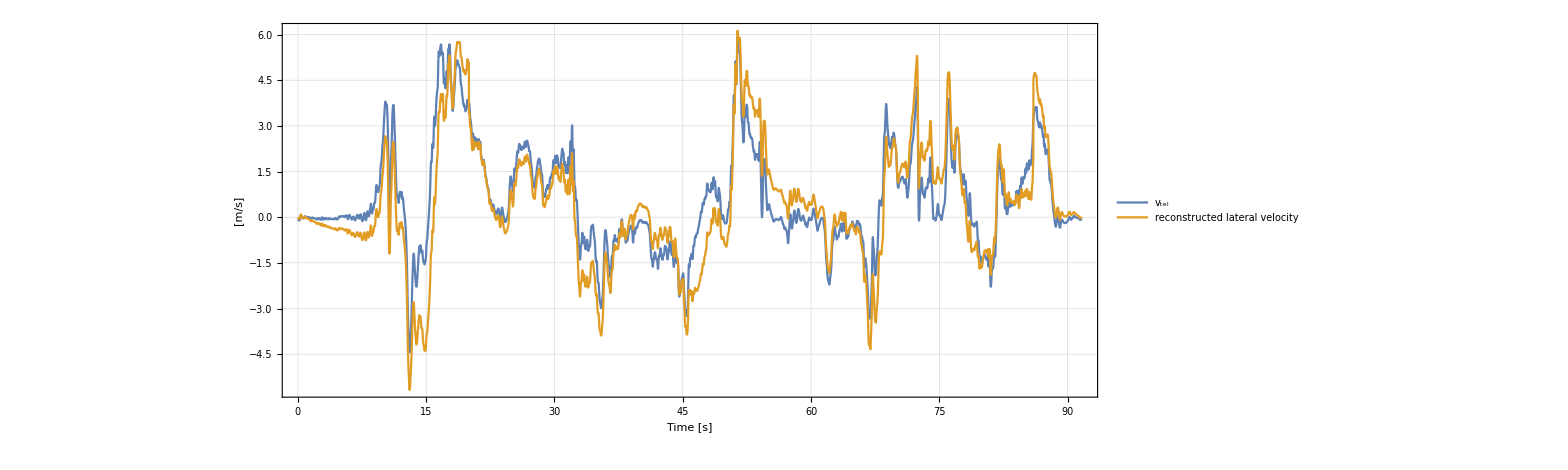

```mathematica
latVel1= Accumulate[latVelDottel-HighpassFilter[latVelDottel,100,9000,SampleRate->100]-Mean[latVelDottel]]/100;
latVel2=latVel1-LowpassFilter[latVel1,0.1,9000,SampleRate->100];
latVelrec = Join[latVel1[[1;;2000]],latVel2[[2001;;8600]],latVel1[[8601;;]]];
ListLinePlot[{Transpose[{time,vtel}],Transpose[{time,latVel1}]},PlotLegends->Placed[{"v_tel","latVel1"},Top],ImageSize->2000,AspectRatio->0.3,PlotRange->All,Frame->True,FrameLabel->{"Time [s]","[m/s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
ListLinePlot[{Transpose[{time,vtel}],Transpose[{time,latVel2}]},PlotLegends->Placed[{"v_tel","latVel2"},Top],ImageSize->2000,AspectRatio->0.3,PlotRange->All,Frame->True,FrameLabel->{"Time [s]","[m/s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
ListLinePlot[{Transpose[{time,vtel}],Transpose[{time,latVelrec}]},PlotLegends->Placed[{"v_tel","reconstructed lateral velocity"},Top],ImageSize->2000,AspectRatio->0.3,PlotRange->All,Frame->True,FrameLabel->{"Time [s]","[m/s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

## Lateral acceleration study

```mathematica
aySmooth =LowpassFilter[aytel,1,SampleRate->100] ;
aySmoothAbs = Abs[aySmooth];
ayNoStraight = aySmoothAbs-Table[10,Length[aySmoothAbs]];
```

Absolute value of the lateral velocity

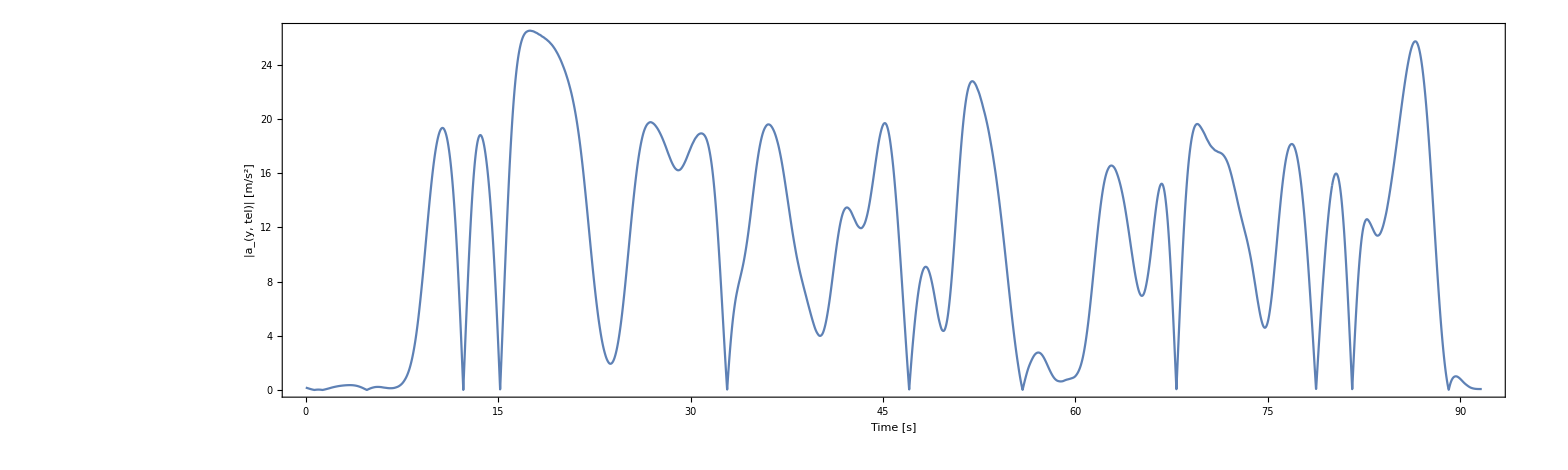

```mathematica
ListLinePlot[Transpose[{time,aySmoothAbs}],ImageSize->2000,AspectRatio->0.3,Frame->True,FrameLabel->{"Time [s]","|a_(y, tel)| [m/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
```

We can subtract 10 m/s^2 to account for an error of the estimate of the lateral velocity during straight lines

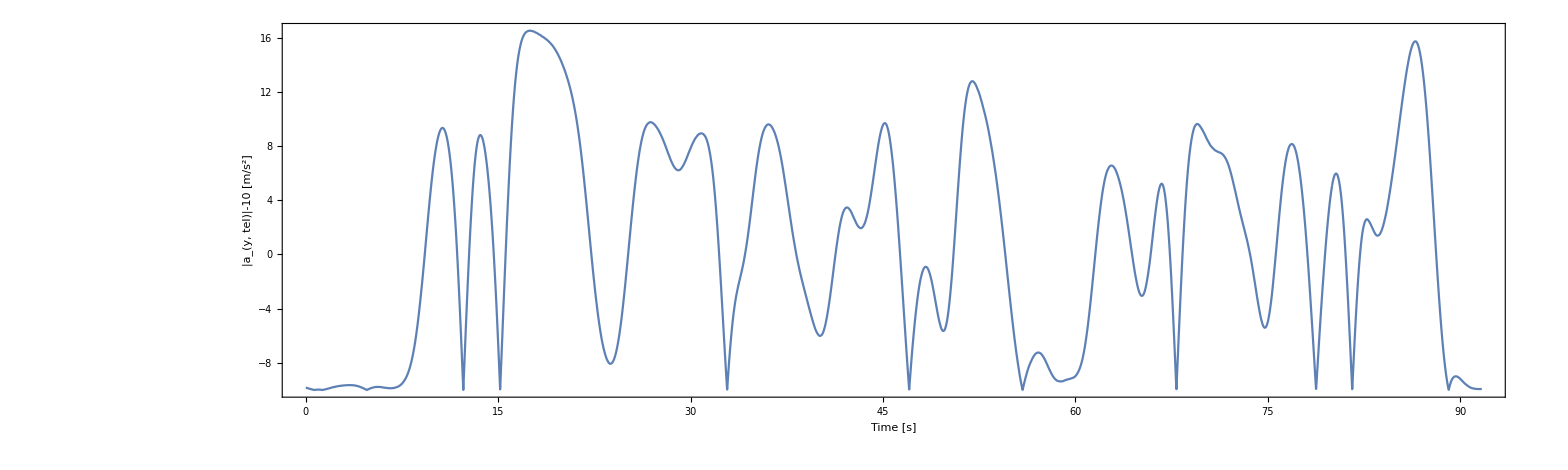

```mathematica
ListLinePlot[Transpose[{time,ayNoStraight}],ImageSize->2000,AspectRatio->0.3,Frame->True,FrameLabel->{"Time [s]","|a_(y, tel)|-10 [m/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
```

In the  intervals in which the function plotted is above the time axis, the vehicle is in a turn; when the function is beneath the time axis, the vehicle is on a straight line. For ease of visualization, in the next plot high values correspond to curves and low values to straight lines.

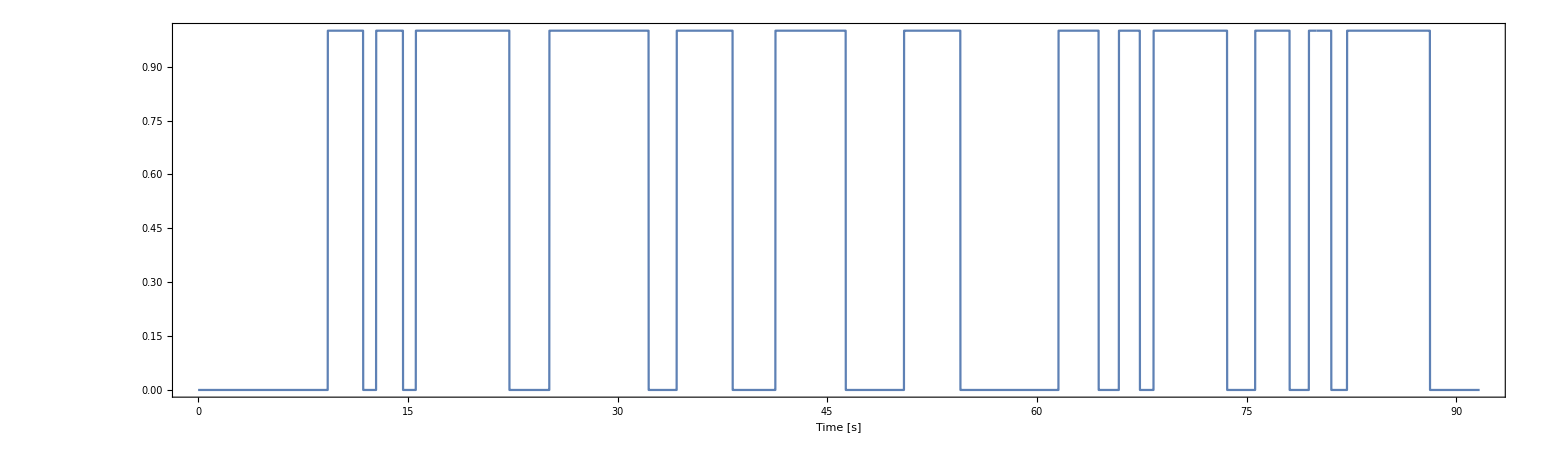

```mathematica
aySign = 0.5*(Sign[ayNoStraight]+1);
ListLinePlot[Transpose[{time,aySign}],ImageSize->2000,AspectRatio->0.3,Frame->True,FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1}]
```

```mathematica
curves = Select[Range[2,Length[aySign]],aySign[[#-1;;#]]=={0.,1.}&];
straights = Select[Range[2,Length[aySign]],aySign[[#-1;;#]]=={1.,0.}&];
curves = Flatten[{curves,Length[time],Length[time]}];
```

Another plot for ease of comprehension: blue lines indicate the vehicle entering the curves, while yellow lines the vehicle exiting the curves.

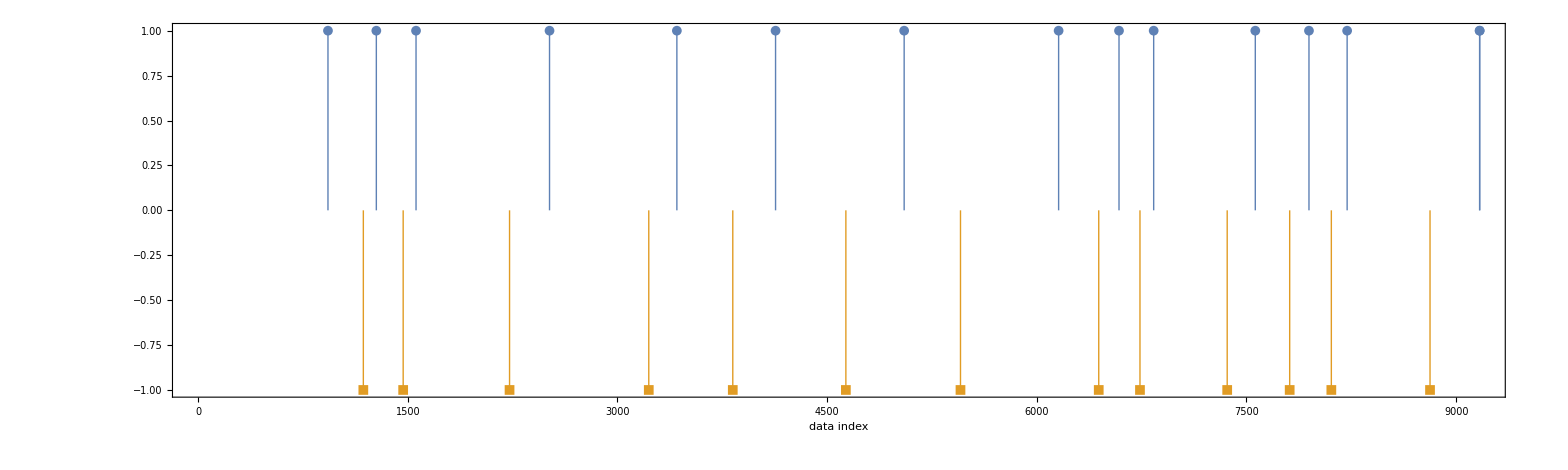

```mathematica
ListPlot[{
Transpose[{curves,Table[1,Length[curves]]}],Transpose[{straights,Table[-1,Length[straights]]}]
},ImageSize->2000,AspectRatio->0.3,Filling -> Axis, PlotMarkers->{Automatic, 10},FillingStyle->Thick,Frame->True,FrameLabel->{"data index"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids100,ygrids1}]
```

## Acceleration study

Confirmation of equation 3.26-3.27 page 73 SVD

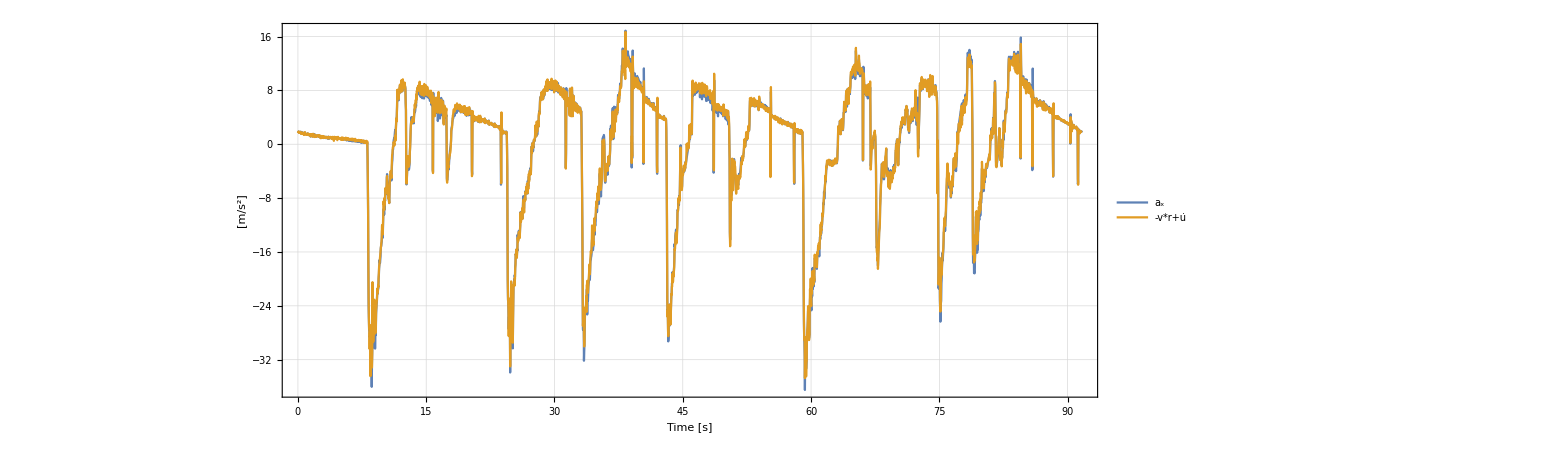

```mathematica
Plot[{ax[t],-v[t]*r[t]+u'[t]},{t,0,Last[time]},PlotLegends->Placed[{"a_x","-v*r+u̇"},Top],ImageSize->3000,AspectRatio->0.3,Frame->True,FrameLabel->{"Time [s]","[m/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
```

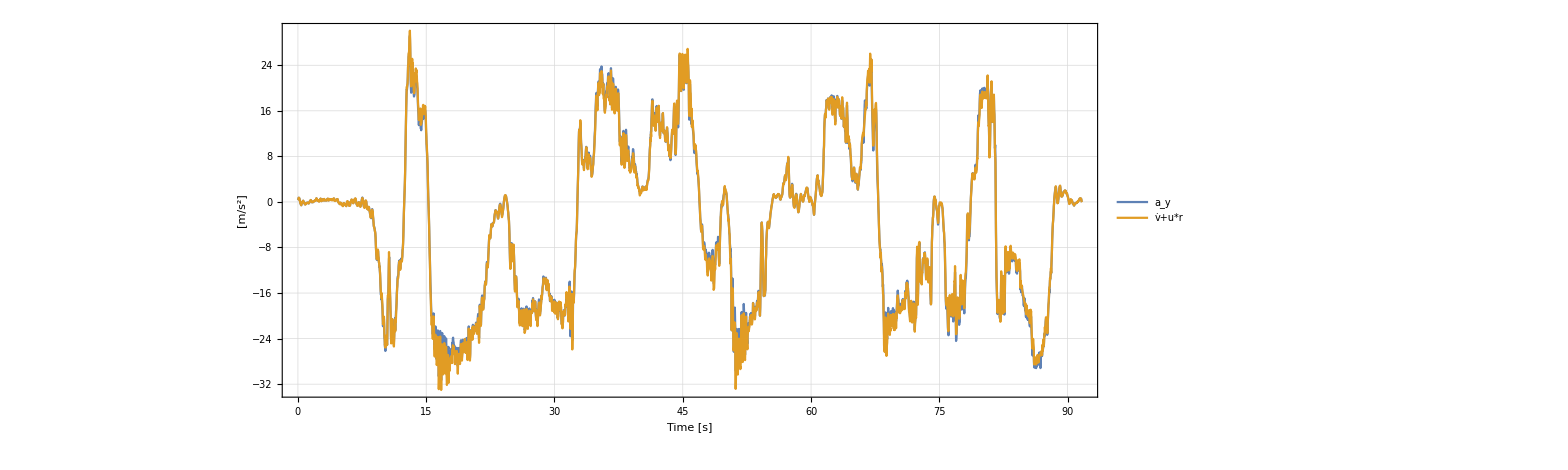

```mathematica
Plot[{ay[t],v'[t]+u[t]*r[t]},{t,0,Last[time]},PlotLegends->Placed[{"a_y","v̇+u*r"},Top],ImageSize->3000,AspectRatio-> 0.3,Frame->True,FrameLabel->{"Time [s]","[m/s^2]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids5}]
```

Equation derived from (3.26 - 3.27) page 74 using (3.16) page 73 SVD
(max step reached for initial condition on t<10)

```mathematica
sol = First[βsol/.NDSolve[{u[t]*βsol'[t]+βsol[t]*(ax[t]+v[t]*r[t]) == ay[t]-u[t]*r[t],βsol[40]== β[40]},βsol, {t,0,Last[time]},InterpolationOrder->1]];
```

To get the InterpolatingFunction points, so we can use ListLinePlot, we can observe sol["Methods"]

{"Coordinates","DerivativeOrder","Domain","ElementMesh","Evaluate","GetPolynomial","Grid","InterpolationMethod","InterpolationOrder","MethodInformation","Methods","OutputDimensions","Periodicity","PlottableQ","Properties","QuantityUnits","Unpack","ValuesOnGrid"}

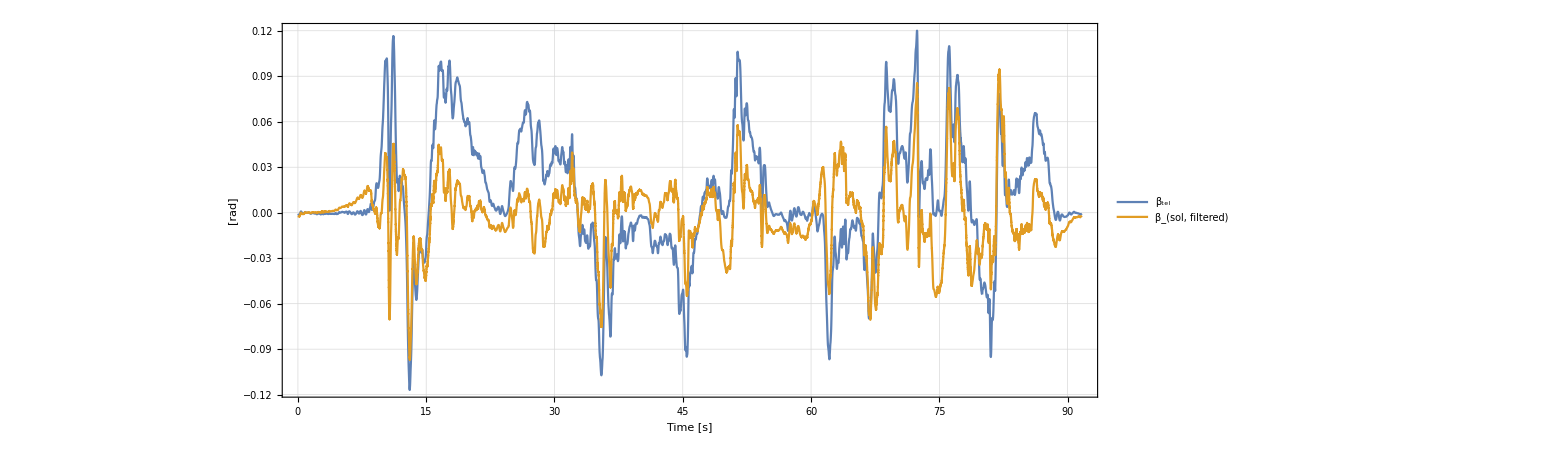

```mathematica
solValues=sol@ValuesOnGrid[];
solβ = solValues-LowpassFilter[solValues,0.01,9000,SampleRate->100];
ListLinePlot[{Transpose[{time,βtel}],Transpose[{Flatten[sol@Coordinates[]],solβ}]},PlotLegends->Placed[{"β_tel","β_(sol, filtered)"},Top],ImageSize->2000,AspectRatio->0.3,PlotRange->All,Frame->True,FrameLabel->{"Time [s]","[rad]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids001}]
```

Not a good numerical solution, compared to gathered data

## Circuit study

```mathematica
velxDir=ufil*Cos[yawfil]-vfil*Sin[yawfil];
velyDir=ufil*Sin[yawfil]+vfil*Cos[yawfil];
xCircuitDir=-Accumulate[velxDir]/100;
yCircuitDir=-Accumulate[velyDir]/100;
velxInv = Reverse[velxDir];
velyInv = Reverse[velyDir];
xCircuitInv = Accumulate[velxInv]/100;
yCircuitInv = Accumulate[velyInv]/100;
```

Circuit reconstruction using coordinates derived through longitudinal velocity u and yaw angle ψ. Actual result obtained as an average of clockwise and counterclockwise computations.

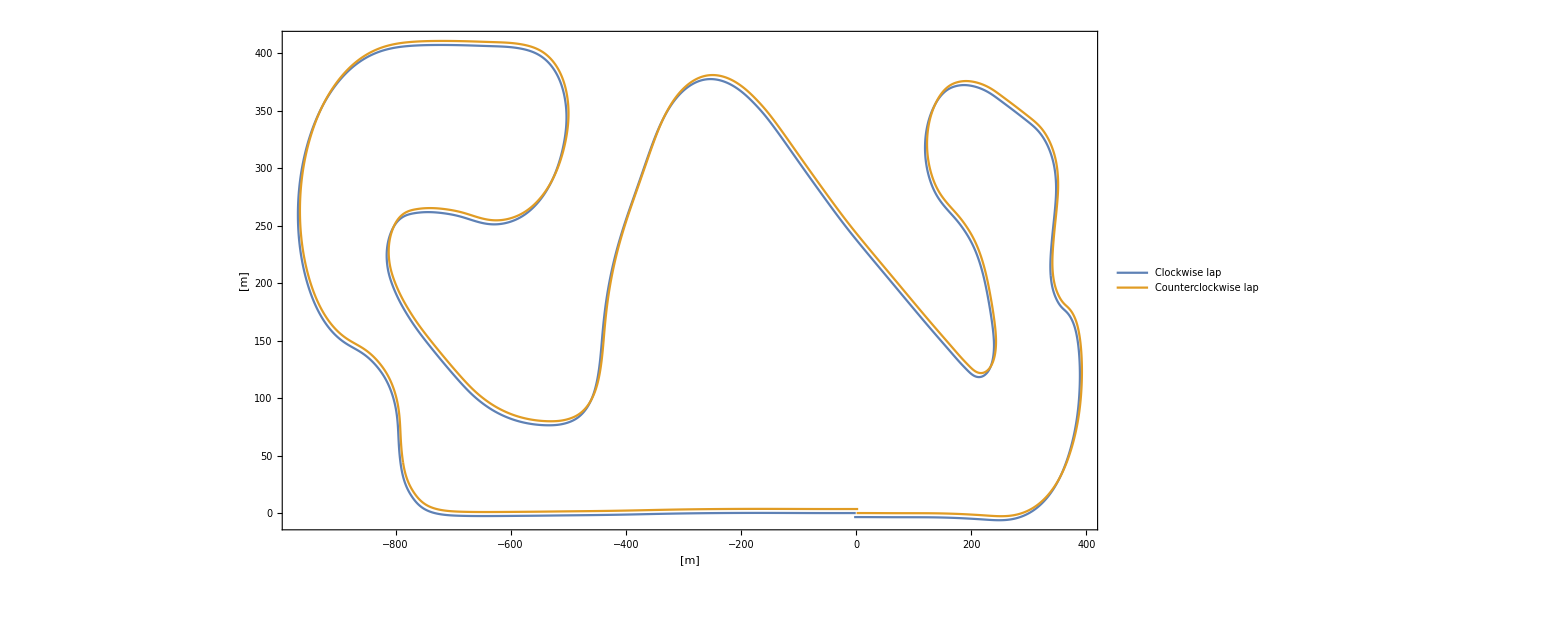

```mathematica
ListLinePlot[{Transpose[{xCircuitDir,yCircuitDir}],Transpose[{xCircuitInv,yCircuitInv}]},PlotStyle->{Thick},PlotLegends->Placed[{"Clockwise lap","Counterclockwise lap"},Top],ImageSize->2000,AspectRatio->Automatic,Frame->True,FrameLabel->{"[m]","[m]"},LabelStyle->Directive[Black,Bold,Large]]
```

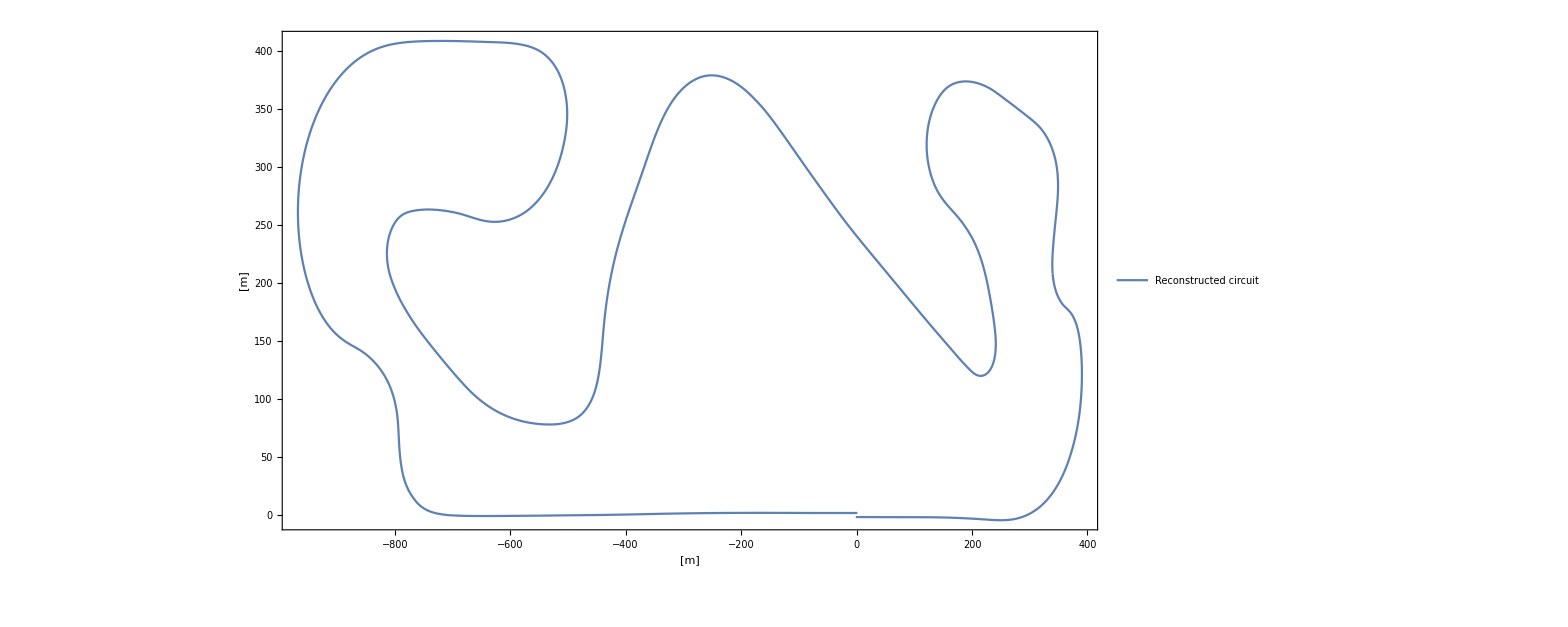

```mathematica
xCircuit =(xCircuitDir+Reverse[xCircuitInv])/2;
yCircuit = (yCircuitDir+Reverse[yCircuitInv])/2;
ListLinePlot[Transpose[{xCircuit,yCircuit}],PlotLegends->Placed[{"Reconstructed circuit"},Top],ImageSize->2000,AspectRatio->Automatic,Frame->True,FrameLabel->{"[m]","[m]"},LabelStyle->Directive[Black,Bold,Large]]
```

Velocity center C coordinates (S, R) in the vehicle axis system, and their derivatives

```mathematica
S = -vfil/rfil;
R = ufil/rfil;
RDot = (axfil-rfil^2*S-rDotfil*R)/rfil;
SDot = (ayfil-rfil^2*R+rDotfil*S)/rfil;
```

Fixed and moving centrodes σ_f and σ_m

```mathematica
xf=aySign*(xCircuit-S*Cos[yawfil]+R*Sin[yawfil]);
yf=aySign*(yCircuit-S*Sin[yawfil]-R*Cos[yawfil]);
```

```mathematica
xm[t_] :=aySign*(xCircuit[[t]]-S*Cos[yawfil[[t]]]+R*Sin[yawfil[[t]]]);
ym[t_]:=aySign*(yCircuit[[t]]-S*Sin[yawfil[[t]]]-R*Cos[yawfil[[t]]]);
```

Radius and center of the inflection circle

```mathematica
d = Sqrt[(RDot^2+SDot^2)/(rfil^2)];
di = RDot/rfil;
dj = -SDot/rfil;
dx = di*Cos[yawfil]-dj*Sin[yawfil];
dy = di*Sin[yawfil]+dj*Cos[yawfil];
```

```mathematica
GCi = S;
GCj = R;
xC= aySign*(xCircuit-GCi*Cos[yawfil]+GCj*Sin[yawfil]);
yC =aySign*(yCircuit-GCi*Sin[yawfil]-GCj*Cos[yawfil]);
```

```mathematica
centerx = xC-dx/2;
centery = yC-dy/2;
```

```mathematica
circ = Table[{centerx+d/2*Cos[a],centery+d/2*Sin[a]},{a,0,2 π,N[(360/100)*Degree]}];
circ2 = Table[{xf+Cos[a],yf+Sin[a]},{a,0,2 π,0.05}];
```

Entire circuit plot

```mathematica
Manipulate[
		ListPlot[{
				Transpose[{aySign*xCircuit,aySign*yCircuit}],
				Transpose[{xf,yf}],
				Transpose[{xm[t],ym[t]}]},
				   PlotLegends->Placed[SwatchLegend[{"Circuit","Fixed centrode","Moving centrode","Inflection circle"},
							LegendMarkerSize->15,LegendMarkers->"Bubble",LegendLabel->Style["Curves",20]],
								Left],
				   ImageSize->Full,
				   AspectRatio->Automatic,
				   PlotRange->{{-1000,550},{-200,450}}
		],
{{t,1,"Time"},1,Length[time],50,AnimationRate->100,Appearance->"Open"}
]
(*sometimes the plot does not show right away for unexplained reasons (performances might be the culprit): evaluate once more if needed*)
```

Since the plot above can be a little confusing (and slow), here another one is shown, where the user can select the desired curve to observe

```mathematica
plotx = {{-850,-600},{-920,-780},{-1000,-700},{-650,-500},{-830,-720},{-700,-400},{-400,-100},{170,250},{50,250},{100,250},{250,360},{320,400},{200,450}};
ploty={{0,200},{0,140},{100,500},{230,430},{180,280},{5,250},{150,400},{100,180},{100,280},{250,400},{250,350},{180,250},{-50,200}};
```

```mathematica
Manipulate[
	curve = curves[[c]];;straights[[c]]-1;
	limit = {plotx[[c]],ploty[[c]]};
	Animate[
		ListPlot[{
				Transpose[{(aySign*xCircuit)[[curve]],(aySign*yCircuit)[[curve]]}],
				Transpose[{xf[[curve]],yf[[curve]]}],
				Transpose[{xm[t][[curve]],ym[t][[curve]]}],
				Transpose[{circ[[All,1,t]],circ[[All,2,t]]}],
				Transpose[{circ2[[All,1,t]],circ2[[All,2,t]]}]
				},
				   PlotLegends->Placed[SwatchLegend[{"Circuit","Fixed centrode","Moving centrode","Inflection circle"},
							LegendMarkerSize->15,LegendMarkers->"Bubble",LegendLabel->Style["Curves",20]],
								Left],
				   ImageSize->500,
				   AspectRatio->Automatic,
				   PerformanceGoal->"Speed",
				   PlotRange->limit
				   ],
		{{t,curves[[c]]+100,"Time"},curves[[c]],straights[[c]]-1,1,AnimationRate->5},
		AnimationRepetitions->1,
		AnimationRunning->False
	],
	{{c,1,"Curve"},1,Length[curves]-2,1,ControlType->SetterBar,Appearance-> "Vertical"},
	Paneled->False,
	ControlPlacement->Left
]
```

## g-g plot

```mathematica
g = 9.81;
ch=ConvexHull[Transpose[{aytel/g,axtel/g}]];
chf=Transpose[{aytel/g,axtel/g}][[ch]];
chf = Join[chf,{First[chf]}]; 
(* the following is to close the hull, if needed *)
ListLinePlot[chf, PlotRange->All,AspectRatio->Automatic,AxesStyle->Medium];
```

```mathematica
Manipulate[
		   car  = 1;;pos;
		   quot = Quotient[pos,705];
		   index = quot+1;;quot+2;
		   curve = curves[[quot+1]];;curves[[quot+2]];
		   circuit = Transpose[{xCircuit,yCircuit}];
		   Row[{
			Show[
				ListLinePlot[chf],
				ListPlot[
						Transpose[{ayfil[[car]]/g,axfil[[car]]/g}],
						PlotStyle->Directive[ColorData["HTML"]["Red"],AbsolutePointSize[7]],
						PerformanceGoal->"Speed",
						PlotLegends->Placed[SwatchLegend[{"evolution"},LegendMarkerSize->15,LegendMarkers->"Bubble",LegendLabel->Style["Curves",20]],Top]
				],
			ListPlot[
					Transpose[{ayfil/g,axfil/g}],
					PlotStyle->{ColorData["HTML"]["DarkGray"]},
					PerformanceGoal->"Speed",
					PlotLegends->Placed[SwatchLegend[{"g-g plot"},LegendMarkerSize->15,LegendMarkers->"Bubble"],Top]
			],
			ImageSize->750,
			AspectRatio->1,
			PlotRange->{{-3.5,3.5},{-4,2}},
			Frame-> True,
			FrameLabel->{{"← Longitudinal acceleration →","← Longitudinal acceleration →"},{"← Left Curve/ Right Curve →","← Left Curve/ Right Curve →"}},
			LabelStyle->Directive[Black,Bold,Large]
			]
		,
			Show[
				ListLinePlot[Transpose[{xCircuit,yCircuit}],ImageSize->500,AspectRatio->Automatic],
				Graphics[{
						PointSize[0.02],
						Green,
						Point[circuit[[pos]] ],
						PlotLegends->Placed[{"real-time \n position"},Top]
				}]
			]
	}],
{{pos,1,"Position"},1,Length[axfil],25,AnimationRate->50},Paneled->False
]
```

Plot to link the position of the vehicle in the circuit with the absolute values of the lateral acceleration

```mathematica
Manipulate[
circuit = Transpose[{xCircuit,yCircuit}];
plot=Abs[LowpassFilter[aytel,1,SampleRate->100]]-10;
point = {time[[pos]]*100,plot[[pos]]};
	Row[{
	Show[
		ListLinePlot[plot,ImageSize->500,PlotLabel->"|a_(y, fil)-10|"],
		Graphics[{
				PointSize[0.02],
				Green,
				Point[point ],
				PlotLegends->Placed[{"real-time \n position"},Top]
	}]
	],
	Show[
		ListLinePlot[Transpose[{xCircuit,yCircuit}],ImageSize->500,AspectRatio->Automatic,ImageSize->500],
		Graphics[{
				PointSize[0.02],
				Green,
				Point[circuit[[pos]] ],
				PlotLegends->Placed[{"real-time \n position"},Top]
		}]
	]
}],
{{pos,1,"Position"},1,Length[axfil],50,AnimationRate->200}
]
```

## Polar study - example with 5^th curve

We can already see from the initial plot (before starting the animation) that the curve considered is not approached in an optimal way by the driver.
As a matter of fact, the fixed and moving centrodes are not “quite good” in terms of what is described  in Chapter 5.2.1 of The Science of Vehicle  Dynamics (M. Guiggiani, 2018).
Further analysis are presented in the attached report.

```mathematica
Manipulate[

instants  = 1;;t;
vehicle ={xCircuit[[t]],yCircuit[[t]]};
turn = curves[[5]];;straights[[5]]-1;

Row[{
	Show[
		ListPlot[{
				Transpose[{(aySign*xCircuit)[[turn]],(aySign*yCircuit)[[turn]]}],
				Transpose[{xf[[turn]],yf[[turn]]}],
				Transpose[{xm[t][[turn]],ym[t][[turn]]}],
				Transpose[{circ[[All,1,t]],circ[[All,2,t]]}],
				Transpose[{circ2[[All,1,t]],circ2[[All,2,t]]}]
				}],
		Graphics[{
				PointSize[0.02],
				Black,
				Point[vehicle],
				PlotLegends->Placed[{"real-time \n position"},Top]
				}],
		   ImageSize->600,
		   AspectRatio->Automatic,
		   PerformanceGoal->"Speed",
		   PlotRange->{plotx[[5]],ploty[[5]]}
		],
Show[
	ListLinePlot[chf],
	ListPlot[
			Transpose[{ayfil[[turn]]/g,axfil[[turn]]/g}],
			PlotStyle->Directive[ColorData["HTML"]["DarkGray"],AbsolutePointSize[4]],
			PerformanceGoal->"Speed"
			],
	Graphics[{
			AbsolutePointSize[6],
			Red,
			Point[{ayfil[[t]]/g,axfil[[t]]/g}],
			PlotLegends->Placed[{"real-time \n position"},Top]
			}],
	ImageSize->600,
	AspectRatio->1,
	PlotRange->{{0.5,2.5},{-2,2}},
	Frame-> True,
	FrameLabel->{{"← Longitudinal acceleration →","← Longitudinal acceleration →"},{"← Left Curve/ Right Curve →","← Left Curve/ Right Curve →"}},
	LabelStyle->Directive[Black,Bold,Large]
	]
},Spacer[100]],
{{t,curves[[5]]+25,"Time"},curves[[5]],straights[[5]]-1,1,AnimationRate->5}
]
```

## Comparison of simulation and real track telemetries

## Importing data

List of available files.

```mathematica
circuits = FileNames["*.xls"];
Transpose[{Range[Length[circuits]],circuits}]//TableForm
```

1 | Gp2_Barcellona_L1_SIMULATORE.xls
2 | Gp2_Barcellona_L1.xls
3 | Gp2_monza_L1.xls

Here we choose the second file, containing telemetry data from a lap of a real vehicle on the circuit

```mathematica
choosenCircuit = 2;
LapsReal = Import[circuits[[choosenCircuit]],{"Sheets"}];
```

```mathematica
totalLaps=Length[LapsReal]
```

1

```mathematica
lap = 1;
```

```mathematica
readings= Import[circuits[[choosenCircuit]],{"Data",lap}];
columns =DeleteDuplicates[ Flatten[Map[Position[readings,#]&, {
"Time",
"speed","Speed","SpeedOverGround","Velocita",
"RawAx","AX","Acc_Long","ACC_X",
"RawAy","AY","Acc_Lat","ACC_Y",
"gyro_z","omega_z_vettura","Vel_Imb","YawRate","YAW_RATE",
"steer","Steer","Angolo_Sterzo","steerAngleWheels","FL_TOE",
"beta","BodySlipAngle","VehicleBeta",
"Dist","dist","LAP_DI","LAP_DIST"
}]]];
(*
Part and Span used because Flatten mixes row and column indexes; this way the list will contain only the column indications
*)
```

```mathematica
(*to check that it's imported row by row: Import[circuits[[choosenCircuit]],{"Data", lap, 1, columns}]*)
rawDatareal = Import[circuits[[choosenCircuit]],{"Data",lap,All,columns}];
```

```mathematica
channelsReal = Transpose[Drop[rawDatareal,1]];
```

```mathematica
{timeReal,urawreal,axrawreal,ayrawreal,rrawreal,δrawreal,βrawreal}=channelsReal[[1;;7]];
```

## Comparison plots

In all the plots below, we can notice that data gathered from the real life lap is delayed of about 1s. Except for this difference, examined in depth in the report, all data are coherent with the studied track.

The longitudinal velocity in the two cases are very similar.

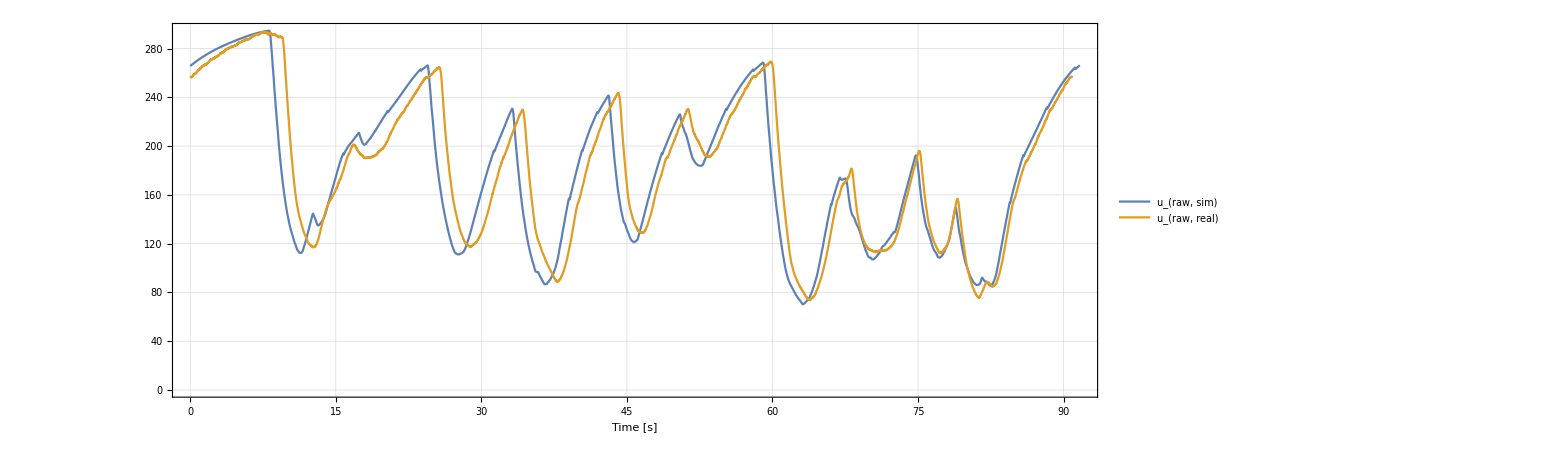

```mathematica
ListLinePlot[{Transpose[{time,uraw}],Transpose[{timeReal,urawreal}]},Frame-> True,FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids50},PlotRange->All,ImageSize->2000,AspectRatio->0.3,PlotLegends->Placed[{"u_(raw, sim)","u_(raw, real)"},Top]]
```

Once again, telemetry data for the real case are similar to the simulation.

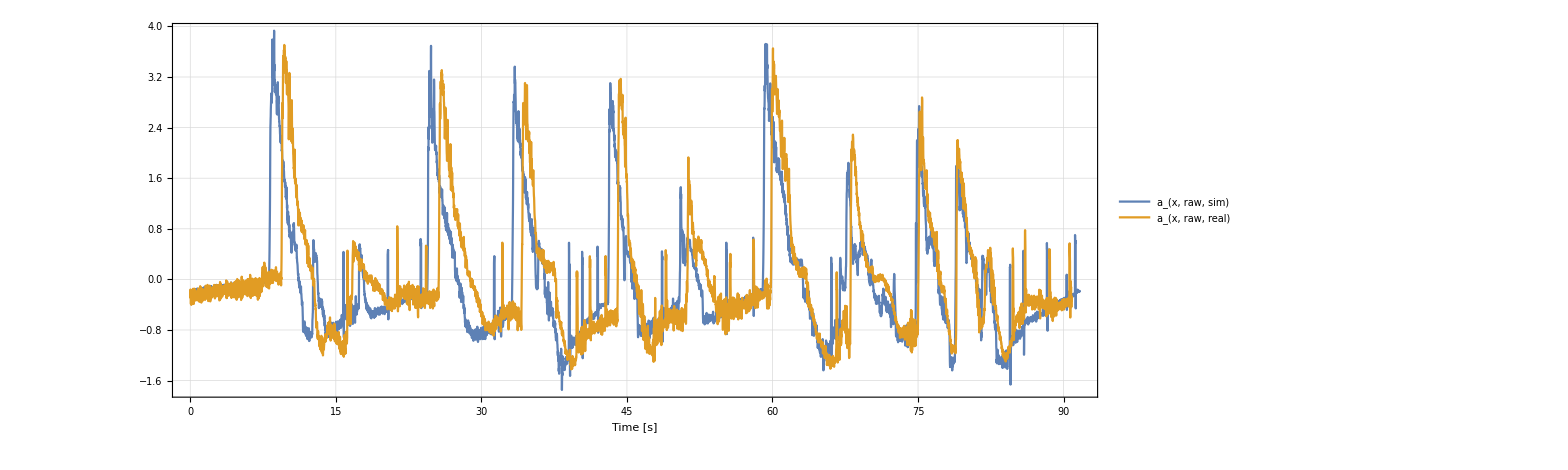

```mathematica
ListLinePlot[{Transpose[{time,axraw}],Transpose[{timeReal,axrawreal}]},Frame-> True,FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1},PlotRange->All,ImageSize->2000,AspectRatio->0.3,PlotLegends->Placed[{"a_(x, raw, sim)","a_(x, raw, real)"},Top]]
```

Except for the delay, lateral acceleration data are almost overlapping.

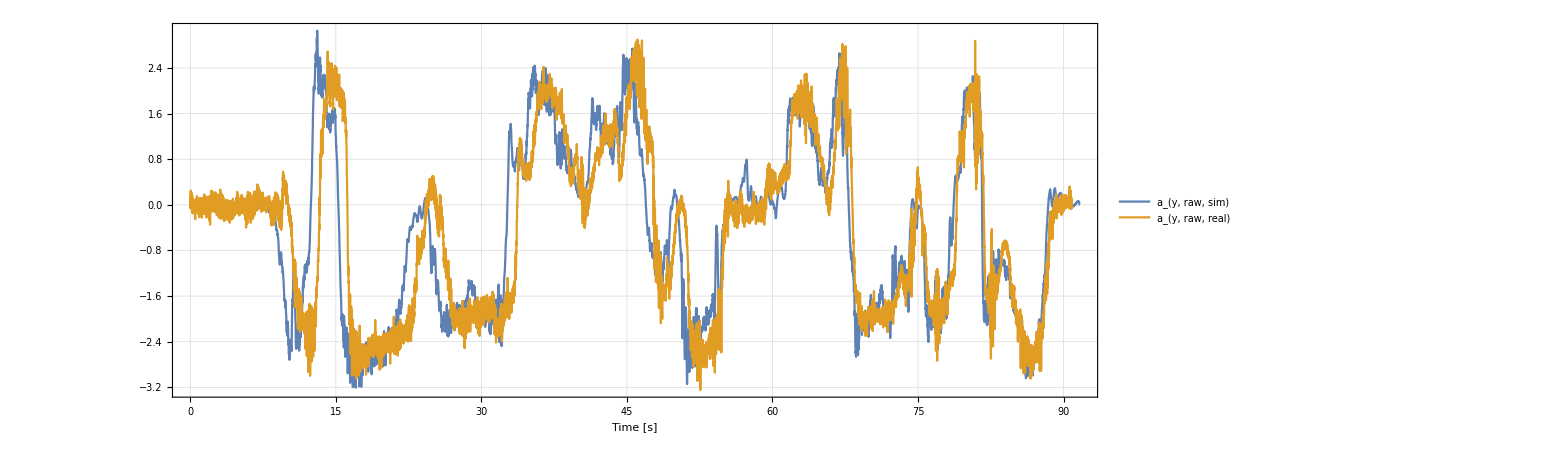

```mathematica
ListLinePlot[{Transpose[{time,ayraw}],Transpose[{timeReal,ayrawreal}]},Frame-> True,FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1},PlotRange->All,ImageSize->2000,AspectRatio->0.3,PlotLegends->Placed[{"a_(y, raw, sim)","a_(y, raw, real)"},Top]]
```

Observing the yaw rate data, we can see that in the real case measurements are taken with an inverse sign respect to the simulation, and in degrees instead of radians (to show this well enough, the real yaw rate is converted).

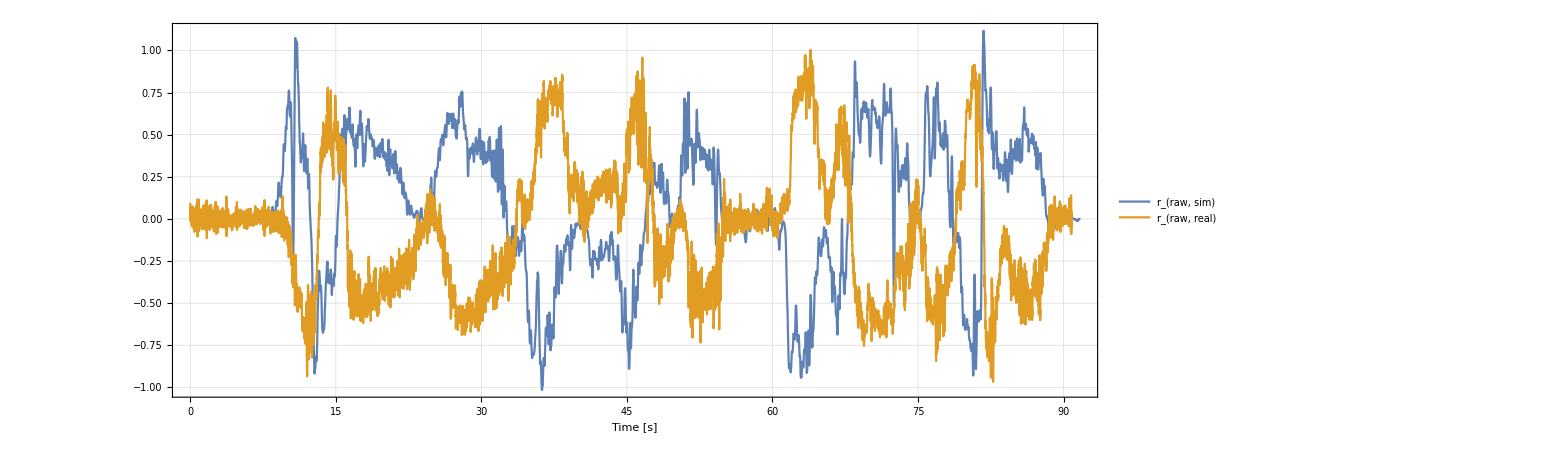

```mathematica
ListLinePlot[{Transpose[{time,rraw}],Transpose[{timeReal,rrawreal*Degree}]},PlotRange->All,ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1},PlotLegends->Placed[{"r_(raw, sim)","r_(raw, real)"},Top]]
```

We can see that the steer angle is measured with an opposite sign in the two cases. Moreover, in the real case the signal presents a lower intensity.

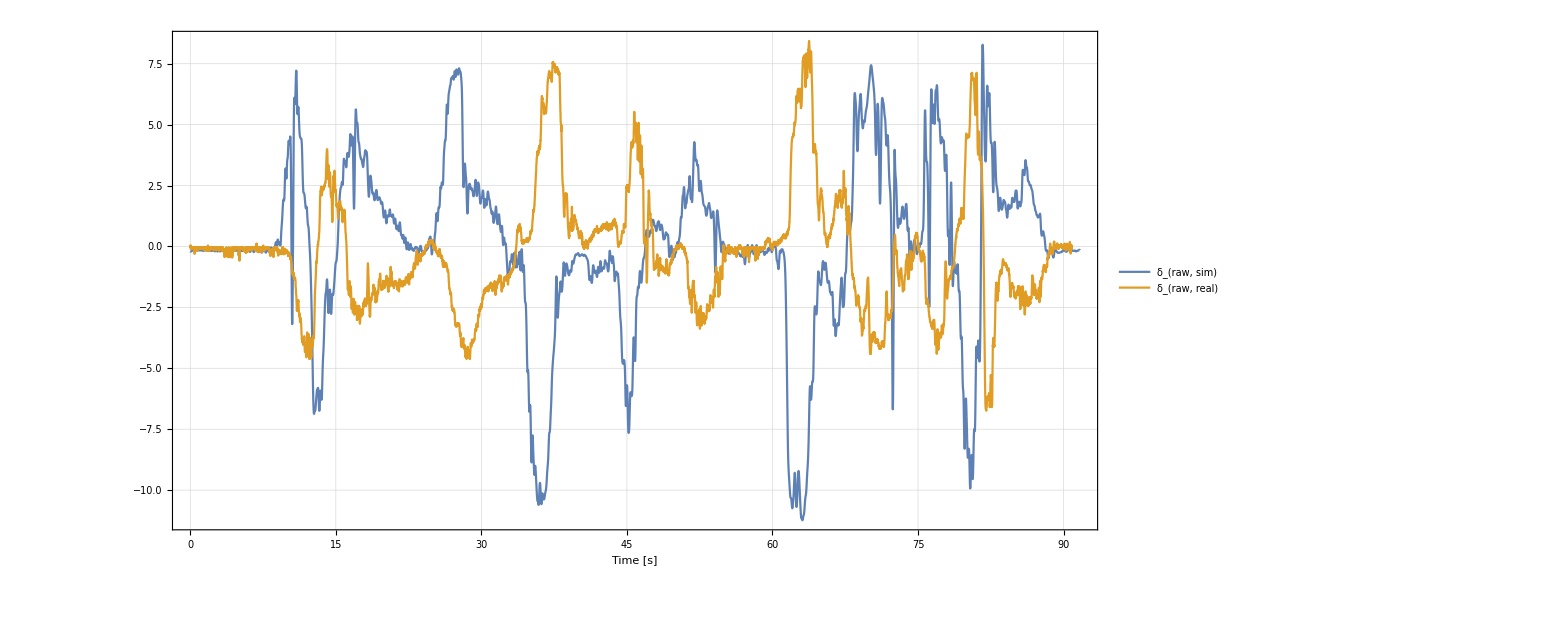

```mathematica
ListLinePlot[{Transpose[{time,δraw}],Transpose[{timeReal,δrawreal}]},PlotRange->All,ImageSize->2000,AspectRatio->Automatic,Frame-> True,FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids1},PlotLegends->Placed[{"δ_(raw, sim)","δ_(raw, real)"},Top]]
```

Measurements of the slip angle β show significant differences.

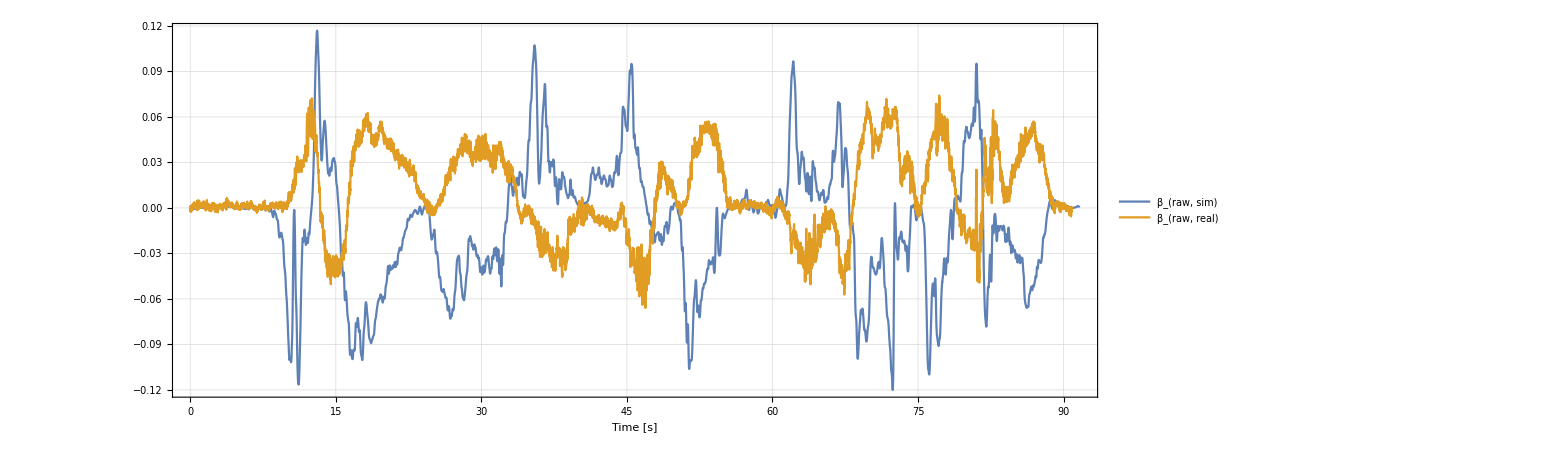

```mathematica
ListLinePlot[{Transpose[{time,βraw}],Transpose[{timeReal,βrawreal*Degree}]},PlotRange -> All, ImageSize->2000,AspectRatio->0.3,Frame-> True,FrameLabel->{"Time [s]"},LabelStyle->Directive[Black,Bold,Large],GridLines->{xgrids,ygrids001},PlotLegends->Placed[{"β_(raw, sim)","β_(raw, real)"},Top]]
```